```mathematica
Exit[]
```

# Black Holes Scalarization - Complex Field

## Generalise results for BH scalarization to two degrees of freedom.

## Field Equations

### Call in the Coordinate-Dep. Tensor package, define coordinates and metric

```mathematica
<<xAct`xCoba`;
<<xAct`TexAct`;
DefManifold[MC,4,IndexRange[a,n]]
DefChart[sspher,MC,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Purple]

DefScalarFunction[A]
DefScalarFunction[B]
DefScalarFunction[F]
DefScalarFunction[X]
DefScalarFunction[T]
DefConstantSymbol[α]
DefConstantSymbol[β]
DefConstantSymbol[κ]
DefConstantSymbol[η]

met=CTensor[DiagonalMatrix[{- A[r[]], (B[r[]])^-1,r[]^2,r[]^2Sin[θ[]]^2}],{-sspher,-sspher}];
SetCMetric[met,sspher,SignatureOfMetric->{3,1,0}];
CD=CovDOfMetric[met];
MetricCompute[met,sspher,All,Parallelize->True];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.3, {2021,10,28}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold MC.

** DefVBundle: Defining vbundle TangentMC.

** DefChart: Defining chart sspher.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping sspher.

** DefMapping: Defining inverse mapping isspher.

** DefTensor: Defining mapping differential tensor disspher[-a,issphera].

** DefTensor: Defining mapping differential tensor dsspher[-a,ssphera].

** DefBasis: Defining basis sspher. Coordinated basis.

** DefCovD: Defining parallel derivative PDsspher[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDsspher[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDsspher[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDsspher[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDsspher[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpsspher[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownsspher[-a,-b,-c,-d].

** DefScalarFunction: Defining scalar function A.

** DefScalarFunction: Defining scalar function B.

** DefScalarFunction: Defining scalar function F.

** DefScalarFunction: Defining scalar function X.

** DefScalarFunction: Defining scalar function T.

** DefConstantSymbol: Defining constant symbol α.

** DefConstantSymbol: Defining constant symbol β.

** DefConstantSymbol: Defining constant symbol κ.

** DefConstantSymbol: Defining constant symbol η.

### Define all the tensors

ℒ = R-1/2∇_μ ξ∇_ν τ-(β R/2-α 𝒢)τ ξ;
Line Element: ⅆ s^2=-A[r]ⅆ t^2+(ⅆ r^2)/B[r]+r^2 ⅆ Ω^2 ;
The Einstein Tensor: G_ab;
Effective Mass Squared for Field Equation : m_eff^2=β/2 R-α𝒢, 𝒢 the Gauss Bonnet Scalar;
The Stress-Energy tensor :(T^ϕ)_μν+(T^α)_μν+ (T^β)_μν, with :
				(T^ϕ)_μν=∇_μ ξ∇_ν τ-1/2 g_μν∇_α ξ∇^α τ , (T^α)_μν=-α/g g_(μ(ρ)g_(σ)ν)ϵ^κραβ ϵ^σγλτ R_λταβ∇_γ ∇_κ ξ τ, (T^β)_μν= 1/2 β(G_μν-∇_μ ∇_ν +g_μν∇_γ ∇^γ)ξτ.

WARNING: Define tensors without “:=”, it does not work properly otherwise!!!

```mathematica
G[a_,b_]=Einstein[CD][a,b];
𝒢 = ((RicciScalar[CD][])^2-4Ricci[CD][-a,-b]Ricci[CD][a,b]+Riemann[CD][a,b,c,d]Riemann[CD][-a,-b,-c,-d])//ContractBasis;
meffSqrd = β/2 RicciScalar[CD][]-α((RicciScalar[CD][])^2-4Ricci[CD][-a,-b]Ricci[CD][a,b]+Riemann[CD][a,b,c,d]Riemann[CD][-a,-b,-c,-d])//ContractBasis;
TPhi[a_,b_]=
(CD[a]@X[r[]]CD[b]@T[r[]]-1/2 met[a,b]CD[-c]@X[r[]]CD[c]@T[r[]]	
)//ContractBasis;
TBeta[a_,b_] =β(G[a,b](X[r[]]T[r[]])/2-CD[a]@CD[b]@((X[r[]]T[r[]])/2)+met[a,b]CD[-c]@CD[c]@((X[r[]]T[r[]])/2))//ContractBasis;
TAlphaEps[a_,b_] =-1/1 α (
2Symmetrize[met[a,-c]met[-d,b],{c,d}]epsilon[met][e,c,f,g]epsilon[met][d,h,i,l]Riemann[CD][-i,-l,-f,-g]CD[-h]@CD[-e]@((X[r[]]T[r[]])/2)
)//ContractBasis;
SETensor[a_,b_]=TAlphaEps[a,b]+TBeta[a,b]+TPhi[a,b];

Trasfξ = {F[r[]]->X[r[]],F'[r[]]->X'[r[]],F''[r[]]->X''[r[]]};
Trasfτ = {F[r[]]->T[r[]],F'[r[]]->T'[r[]],F''[r[]]->T''[r[]]};
TrasfFinal = {X[r]->ξ[r],X'[r]->ξ'[r],X''[r]->ξ''[r],
			T[r]->τ[r],T'[r]->τ'[r],T''[r]->τ''[r]};
```

## Field Equations

G_μν=κT_μν     with   T_μν=((T^ϕ)_μν+(T^α)_μν+(T^β)_μν) and κ=1
□ϕ = m_eff^2 ϕ

```mathematica
TauEq =CD[-a]@CD[a]@T[r[]]-meffSqrd (T[r[]]);
XiEq =CD[-a]@CD[a]@X[r[]]-meffSqrd X[r[]];
ttEq=G[{0,sspher},{0,-sspher}]-(κ SETensor[{0,sspher},{0,-sspher}]);
rrEq=G[{1,sspher},{1,-sspher}]-κ( SETensor[{1,sspher},{1,-sspher}]);
θθEq=G[{2,sspher},{2,-sspher}]-κ( SETensor[{2,sspher},{2,-sspher}]);
```

#### Final expression for Eq. of Motion to use in the Numerical Integrator

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ]
FinalττEq = TauEq//Expand /.{r[]->r}/.TrasfFinal;
FinalξξEq = XiEq//Expand /.{r[]->r}/.TrasfFinal;
FinalttEq = ttEq//Expand /.{r[]->r}/.TrasfFinal;
FinalrrEq = rrEq//Expand /.{r[]->r}/.TrasfFinal;
FinalθθEq = θθEq//Expand /.{r[]->r}/.TrasfFinal;
GaussBonnet = 𝒢//Expand /.{r[]->r}/.TrasfFinal;

FieldEqs = {FinalttEq,FinalrrEq,FinalθθEq,FinalττEq,FinalξξEq}/.{r[]->r,η->1,κ->1}/.TrasfFinal;
MatrixForm[FieldEqs]
```

```mathematica
FieldEqs =({{-1/r^2+B[r]/r^2+(β ξ[r] τ[r])/(2 r^2)-(β B[r] ξ[r] τ[r])/(2 r^2)+B'[r]/r-(β ξ[r] τ[r] B'[r])/(2 r)-(β B[r] τ[r] ξ'[r])/r+(2 α τ[r] B'[r] ξ'[r])/r^2-1/4 β τ[r] B'[r] ξ'[r]-(6 α B[r] τ[r] B'[r] ξ'[r])/r^2-(β B[r] ξ[r] τ'[r])/r+(2 α ξ[r] B'[r] τ'[r])/r^2-1/4 β ξ[r] B'[r] τ'[r]-(6 α B[r] ξ[r] B'[r] τ'[r])/r^2+1/2 B[r] ξ'[r] τ'[r]+(8 α B[r] ξ'[r] τ'[r])/r^2-β B[r] ξ'[r] τ'[r]-(8 α B[r]^2 ξ'[r] τ'[r])/r^2+(4 α B[r] τ[r] ξ''[r])/r^2-1/2 β B[r] τ[r] ξ''[r]-(4 α B[r]^2 τ[r] ξ''[r])/r^2+(4 α B[r] ξ[r] τ''[r])/r^2-1/2 β B[r] ξ[r] τ''[r]-(4 α B[r]^2 ξ[r] τ''[r])/r^2}, {-1/r^2+B[r]/r^2+(β ξ[r] τ[r])/(2 r^2)-(β B[r] ξ[r] τ[r])/(2 r^2)+(B[r] A'[r])/(r A[r])-(β B[r] ξ[r] τ[r] A'[r])/(2 r A[r])-(β B[r] τ[r] ξ'[r])/r+(2 α B[r] τ[r] A'[r] ξ'[r])/(r^2 A[r])-(β B[r] τ[r] A'[r] ξ'[r])/(4 A[r])-(6 α B[r]^2 τ[r] A'[r] ξ'[r])/(r^2 A[r])-(β B[r] ξ[r] τ'[r])/r+(2 α B[r] ξ[r] A'[r] τ'[r])/(r^2 A[r])-(β B[r] ξ[r] A'[r] τ'[r])/(4 A[r])-(6 α B[r]^2 ξ[r] A'[r] τ'[r])/(r^2 A[r])-1/2 B[r] ξ'[r] τ'[r]}, {(B[r] A'[r])/(2 r A[r])-(β B[r] ξ[r] τ[r] A'[r])/(4 r A[r])-(B[r] A'[r]^2)/(4 A[r]^2)+(β B[r] ξ[r] τ[r] A'[r]^2)/(8 A[r]^2)+B'[r]/(2 r)-(β ξ[r] τ[r] B'[r])/(4 r)+(A'[r] B'[r])/(4 A[r])-(β ξ[r] τ[r] A'[r] B'[r])/(8 A[r])-(β B[r] τ[r] ξ'[r])/(2 r)-(β B[r] τ[r] A'[r] ξ'[r])/(4 A[r])+(α B[r]^2 τ[r] A'[r]^2 ξ'[r])/(r A[r]^2)-1/4 β τ[r] B'[r] ξ'[r]-(3 α B[r] τ[r] A'[r] B'[r] ξ'[r])/(r A[r])-(β B[r] ξ[r] τ'[r])/(2 r)-(β B[r] ξ[r] A'[r] τ'[r])/(4 A[r])+(α B[r]^2 ξ[r] A'[r]^2 τ'[r])/(r A[r]^2)-1/4 β ξ[r] B'[r] τ'[r]-(3 α B[r] ξ[r] A'[r] B'[r] τ'[r])/(r A[r])+1/2 B[r] ξ'[r] τ'[r]-β B[r] ξ'[r] τ'[r]-(4 α B[r]^2 A'[r] ξ'[r] τ'[r])/(r A[r])+(B[r] A''[r])/(2 A[r])-(β B[r] ξ[r] τ[r] A''[r])/(4 A[r])-(2 α B[r]^2 τ[r] ξ'[r] A''[r])/(r A[r])-(2 α B[r]^2 ξ[r] τ'[r] A''[r])/(r A[r])-1/2 β B[r] τ[r] ξ''[r]-(2 α B[r]^2 τ[r] A'[r] ξ''[r])/(r A[r])-1/2 β B[r] ξ[r] τ''[r]-(2 α B[r]^2 ξ[r] A'[r] τ''[r])/(r A[r])}, {-(β τ[r])/r^2+(β B[r] τ[r])/r^2+(β B[r] τ[r] A'[r])/(r A[r])+(2 α B[r] τ[r] A'[r]^2)/(r^2 A[r]^2)-(β B[r] τ[r] A'[r]^2)/(4 A[r]^2)-(2 α B[r]^2 τ[r] A'[r]^2)/(r^2 A[r]^2)+(β τ[r] B'[r])/r-(2 α τ[r] A'[r] B'[r])/(r^2 A[r])+(β τ[r] A'[r] B'[r])/(4 A[r])+(6 α B[r] τ[r] A'[r] B'[r])/(r^2 A[r])+(2 B[r] τ'[r])/r+(B[r] A'[r] τ'[r])/(2 A[r])+1/2 B'[r] τ'[r]-(4 α B[r] τ[r] A''[r])/(r^2 A[r])+(β B[r] τ[r] A''[r])/(2 A[r])+(4 α B[r]^2 τ[r] A''[r])/(r^2 A[r])+B[r] τ''[r]}, {-(β ξ[r])/r^2+(β B[r] ξ[r])/r^2+(β B[r] ξ[r] A'[r])/(r A[r])+(2 α B[r] ξ[r] A'[r]^2)/(r^2 A[r]^2)-(β B[r] ξ[r] A'[r]^2)/(4 A[r]^2)-(2 α B[r]^2 ξ[r] A'[r]^2)/(r^2 A[r]^2)+(β ξ[r] B'[r])/r-(2 α ξ[r] A'[r] B'[r])/(r^2 A[r])+(β ξ[r] A'[r] B'[r])/(4 A[r])+(6 α B[r] ξ[r] A'[r] B'[r])/(r^2 A[r])+(2 B[r] ξ'[r])/r+(B[r] A'[r] ξ'[r])/(2 A[r])+1/2 B'[r] ξ'[r]-(4 α B[r] ξ[r] A''[r])/(r^2 A[r])+(β B[r] ξ[r] A''[r])/(2 A[r])+(4 α B[r]^2 ξ[r] A''[r])/(r^2 A[r])+B[r] ξ''[r]}});
```

Get the system of ODE from the field equations and express it re-naming the metric functions as follows

ⅆ s^2=-x[r]ⅆ t^2+(ⅆ r^2)/y[r]+r^2 ⅆ Ω^2

```mathematica
AlgebSystem=Solve[(FieldEqs)==0,{ξ''[r],τ''[r],A'[r],B'[r],A''[r]}][[1]][[1;;4]]/.{Rule->Subtract}/.{A[r]->x[r],B[r]->y[r],A'[r]->x'[r],B'[r]->y'[r],A''[r]->x''[r],B''[r]->y''[r]}
```

{-(-768 r^3 α ξ[r]+1222+3072 r^5 α^3 β y[r]^4 ξ[r]^3 ξ'[r]^2 τ'[r]^4)/(64 r^7 y[r]-6144 r^3 α^2 y[r] ξ[r] τ[r]-128 r^7 β y[r] ξ[r] τ[r]+522+3072 r^5 α^3 β y[r]^4 ξ[r]^4 τ'[r]^4+36864 r^3 α^4 y[r]^5 ξ[r]^4 τ'[r]^4)+ξ''[r],-1/(528+1)+τ''[r],x'[r]+1/1,y'[r]+(2 r (-8 r^3+303))/1}
 |  |  |  |

## Boundary Conditions

### Perturbative Solution @ Horizon

We will start integrating from the event horizon. Here the functions diverge (A,B) or vanish (σ,ρ). We have to implement appropriate boundary conditions solving the equations in perturbation theory.  
First, we move to the σ-ρ expression for the metric and solve the algebraic system for the relevant functions.

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y,ξ,τ]
```

```mathematica
HorizonSystem = AlgebSystem
```

{-(-768 r^3 α ξ[r]+1222+3072 r^5 α^3 β y[r]^4 ξ[r]^3 ξ'[r]^2 τ'[r]^4)/(64 r^7 y[r]-6144 r^3 α^2 y[r] ξ[r] τ[r]-128 r^7 β y[r] ξ[r] τ[r]+522+3072 r^5 α^3 β y[r]^4 ξ[r]^4 τ'[r]^4+36864 r^3 α^4 y[r]^5 ξ[r]^4 τ'[r]^4)+ξ''[r],-1/(528+1)+τ''[r],x'[r]+1/1,y'[r]+(2 r (-8 r^3+303))/1}
 |  |  |  |

Then, let’s expand them near the horizon.

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
x[r_]:=∑_(i=1)^3 Subscript[a, i](r-1)^i; (*Define all the functions as a power series; n.b. horizon at r=1*)
y[r_] :=∑_(i=1)^3 Subscript[b, i](r-1)^i;(* these definitions will be inserted in the system*)
τ[r_]:=∑_(i=0)^3 Subscript[t, i](r-1)^i;
ξ[r_]:=∑_(i=0)^3 Subscript[e, i](r-1)^i;
```

Hence we solve the equations order by order, getting a proper solution with free parameters the value of the scalar field and the first derivative of σ at the horizon.

```mathematica
HorEqs = Series[{HorizonSystem[[1]](r-1),HorizonSystem[[2]](r-1),HorizonSystem[[3]],HorizonSystem[[4]]},{r,1,3}];
HorEqs1 = Table[SeriesCoefficient[HorEqs[[i]],0],{i,1,3}];
(*HorEqs2 = Table[SeriesCoefficient[HorEqs[[i]],1],{i,1,3}];*)
```

```mathematica
HorEqs1 = Table[SeriesCoefficient[HorEqs[[i]],0],{i,1,4}];
```

```mathematica
HorEqs1
```

{-((-768 α e_0-64 e_1+1536 α β e_0^2 t_0+128 β e_0 e_1 t_0+768 α β e_0 e_1 t_0-96 β^2 e_0 e_1 t_0-256 α e_1^2 t_0+32 β e_1^2 t_0-1152 α β^2 e_0^3 t_0^2-96 β^2 e_0^2 e_1 t_0^2-1152 α β^2 e_0^2 e_1 t_0^2+144 β^3 e_0^2 e_1 t_0^2+384 α β e_0 e_1^2 t_0^2+3072 α^2 β e_0 e_1^2 t_0^2-48 β^2 e_0 e_1^2 t_0^2-768 α β^2 e_0 e_1^2 t_0^2+48 β^3 e_0 e_1^2 t_0^2-256 α^2 e_1^3 t_0^2+64 α β e_1^3 t_0^2-4 β^2 e_1^3 t_0^2+384 α β^3 e_0^4 t_0^3+32 β^3 e_0^3 e_1 t_0^3+576 α β^3 e_0^3 e_1 t_0^3-72 β^4 e_0^3 e_1 t_0^3-192 α β^2 e_0^2 e_1^2 t_0^3-3072 α^2 β^2 e_0^2 e_1^2 t_0^3+24 β^3 e_0^2 e_1^2 t_0^3+768 α β^3 e_0^2 e_1^2 t_0^3-48 β^4 e_0^2 e_1^2 t_0^3+256 α^2 β e_0 e_1^3 t_0^3+3072 α^3 β e_0 e_1^3 t_0^3-64 α β^2 e_0 e_1^3 t_0^3-1152 α^2 β^2 e_0 e_1^3 t_0^3+4 β^3 e_0 e_1^3 t_0^3+144 α β^3 e_0 e_1^3 t_0^3-6 β^4 e_0 e_1^3 t_0^3-48 α β^4 e_0^5 t_0^4-4 β^4 e_0^4 e_1 t_0^4-96 α β^4 e_0^4 e_1 t_0^4+12 β^5 e_0^4 e_1 t_0^4+32 α β^3 e_0^3 e_1^2 t_0^4+768 α^2 β^3 e_0^3 e_1^2 t_0^4-4 β^4 e_0^3 e_1^2 t_0^4-192 α β^4 e_0^3 e_1^2 t_0^4+12 β^5 e_0^3 e_1^2 t_0^4-64 α^2 β^2 e_0^2 e_1^3 t_0^4-1536 α^3 β^2 e_0^2 e_1^3 t_0^4+16 α β^3 e_0^2 e_1^3 t_0^4+576 α^2 β^3 e_0^2 e_1^3 t_0^4-β^4 e_0^2 e_1^3 t_0^4-72 α β^4 e_0^2 e_1^3 t_0^4+3 β^5 e_0^2 e_1^3 t_0^4-3072 α^2 e_0^2 t_1+384 α β e_0^2 t_1-256 α e_0 e_1 t_1+32 β e_0 e_1 t_1+4608 α^2 β e_0^3 t_0 t_1-576 α β^2 e_0^3 t_0 t_1+384 α β e_0^2 e_1 t_0 t_1+3072 α^2 β e_0^2 e_1 t_0 t_1-48 β^2 e_0^2 e_1 t_0 t_1-768 α β^2 e_0^2 e_1 t_0 t_1+48 β^3 e_0^2 e_1 t_0 t_1-512 α^2 e_0 e_1^2 t_0 t_1+128 α β e_0 e_1^2 t_0 t_1-8 β^2 e_0 e_1^2 t_0 t_1-2304 α^2 β^2 e_0^4 t_0^2 t_1+288 α β^3 e_0^4 t_0^2 t_1-192 α β^2 e_0^3 e_1 t_0^2 t_1-3072 α^2 β^2 e_0^3 e_1 t_0^2 t_1+24 β^3 e_0^3 e_1 t_0^2 t_1+768 α β^3 e_0^3 e_1 t_0^2 t_1-48 β^4 e_0^3 e_1 t_0^2 t_1+512 α^2 β e_0^2 e_1^2 t_0^2 t_1+6144 α^3 β e_0^2 e_1^2 t_0^2 t_1-128 α β^2 e_0^2 e_1^2 t_0^2 t_1-2304 α^2 β^2 e_0^2 e_1^2 t_0^2 t_1+8 β^3 e_0^2 e_1^2 t_0^2 t_1+288 α β^3 e_0^2 e_1^2 t_0^2 t_1-12 β^4 e_0^2 e_1^2 t_0^2 t_1+384 α^2 β^3 e_0^5 t_0^3 t_1-48 α β^4 e_0^5 t_0^3 t_1+32 α β^3 e_0^4 e_1 t_0^3 t_1+768 α^2 β^3 e_0^4 e_1 t_0^3 t_1-4 β^4 e_0^4 e_1 t_0^3 t_1-192 α β^4 e_0^4 e_1 t_0^3 t_1+12 β^5 e_0^4 e_1 t_0^3 t_1-128 α^2 β^2 e_0^3 e_1^2 t_0^3 t_1-3072 α^3 β^2 e_0^3 e_1^2 t_0^3 t_1+32 α β^3 e_0^3 e_1^2 t_0^3 t_1+1152 α^2 β^3 e_0^3 e_1^2 t_0^3 t_1-2 β^4 e_0^3 e_1^2 t_0^3 t_1-144 α β^4 e_0^3 e_1^2 t_0^3 t_1+6 β^5 e_0^3 e_1^2 t_0^3 t_1-256 α^2 e_0^2 e_1 t_1^2+64 α β e_0^2 e_1 t_1^2-4 β^2 e_0^2 e_1 t_1^2+256 α^2 β e_0^3 e_1 t_0 t_1^2+3072 α^3 β e_0^3 e_1 t_0 t_1^2-64 α β^2 e_0^3 e_1 t_0 t_1^2-1152 α^2 β^2 e_0^3 e_1 t_0 t_1^2+4 β^3 e_0^3 e_1 t_0 t_1^2+144 α β^3 e_0^3 e_1 t_0 t_1^2-6 β^4 e_0^3 e_1 t_0 t_1^2-64 α^2 β^2 e_0^4 e_1 t_0^2 t_1^2-1536 α^3 β^2 e_0^4 e_1 t_0^2 t_1^2+16 α β^3 e_0^4 e_1 t_0^2 t_1^2+576 α^2 β^3 e_0^4 e_1 t_0^2 t_1^2-β^4 e_0^4 e_1 t_0^2 t_1^2-72 α β^4 e_0^4 e_1 t_0^2 t_1^2+3 β^5 e_0^4 e_1 t_0^2 t_1^2)/(64 b_1-6144 α^2 b_1 e_0 t_0-128 β b_1 e_0 t_0+96 β^2 b_1 e_0 t_0+256 α b_1 e_1 t_0-32 β b_1 e_1 t_0+9216 α^2 β b_1 e_0^2 t_0^2+96 β^2 b_1 e_0^2 t_0^2-144 β^3 b_1 e_0^2 t_0^2-12288 α^3 b_1 e_0 e_1 t_0^2-384 α β b_1 e_0 e_1 t_0^2+48 β^2 b_1 e_0 e_1 t_0^2+576 α β^2 b_1 e_0 e_1 t_0^2-48 β^3 b_1 e_0 e_1 t_0^2+256 α^2 b_1 e_1^2 t_0^2-64 α β b_1 e_1^2 t_0^2+4 β^2 b_1 e_1^2 t_0^2-4608 α^2 β^2 b_1 e_0^3 t_0^3-32 β^3 b_1 e_0^3 t_0^3+72 β^4 b_1 e_0^3 t_0^3+12288 α^3 β b_1 e_0^2 e_1 t_0^3+192 α β^2 b_1 e_0^2 e_1 t_0^3-24 β^3 b_1 e_0^2 e_1 t_0^3-576 α β^3 b_1 e_0^2 e_1 t_0^3+48 β^4 b_1 e_0^2 e_1 t_0^3-256 α^2 β b_1 e_0 e_1^2 t_0^3-3072 α^3 β b_1 e_0 e_1^2 t_0^3+64 α β^2 b_1 e_0 e_1^2 t_0^3+1152 α^2 β^2 b_1 e_0 e_1^2 t_0^3-4 β^3 b_1 e_0 e_1^2 t_0^3-144 α β^3 b_1 e_0 e_1^2 t_0^3+6 β^4 b_1 e_0 e_1^2 t_0^3+768 α^2 β^3 b_1 e_0^4 t_0^4+4 β^4 b_1 e_0^4 t_0^4-12 β^5 b_1 e_0^4 t_0^4-3072 α^3 β^2 b_1 e_0^3 e_1 t_0^4-32 α β^3 b_1 e_0^3 e_1 t_0^4+4 β^4 b_1 e_0^3 e_1 t_0^4+144 α β^4 b_1 e_0^3 e_1 t_0^4-12 β^5 b_1 e_0^3 e_1 t_0^4+64 α^2 β^2 b_1 e_0^2 e_1^2 t_0^4+1536 α^3 β^2 b_1 e_0^2 e_1^2 t_0^4-16 α β^3 b_1 e_0^2 e_1^2 t_0^4-576 α^2 β^3 b_1 e_0^2 e_1^2 t_0^4+β^4 b_1 e_0^2 e_1^2 t_0^4+72 α β^4 b_1 e_0^2 e_1^2 t_0^4-3 β^5 b_1 e_0^2 e_1^2 t_0^4+256 α b_1 e_0 t_1-32 β b_1 e_0 t_1-12288 α^3 b_1 e_0^2 t_0 t_1-384 α β b_1 e_0^2 t_0 t_1+48 β^2 b_1 e_0^2 t_0 t_1+576 α β^2 b_1 e_0^2 t_0 t_1-48 β^3 b_1 e_0^2 t_0 t_1+512 α^2 b_1 e_0 e_1 t_0 t_1-128 α β b_1 e_0 e_1 t_0 t_1+8 β^2 b_1 e_0 e_1 t_0 t_1+12288 α^3 β b_1 e_0^3 t_0^2 t_1+192 α β^2 b_1 e_0^3 t_0^2 t_1-24 β^3 b_1 e_0^3 t_0^2 t_1-576 α β^3 b_1 e_0^3 t_0^2 t_1+48 β^4 b_1 e_0^3 t_0^2 t_1-512 α^2 β b_1 e_0^2 e_1 t_0^2 t_1-6144 α^3 β b_1 e_0^2 e_1 t_0^2 t_1+128 α β^2 b_1 e_0^2 e_1 t_0^2 t_1+2304 α^2 β^2 b_1 e_0^2 e_1 t_0^2 t_1-8 β^3 b_1 e_0^2 e_1 t_0^2 t_1-288 α β^3 b_1 e_0^2 e_1 t_0^2 t_1+12 β^4 b_1 e_0^2 e_1 t_0^2 t_1-3072 α^3 β^2 b_1 e_0^4 t_0^3 t_1-32 α β^3 b_1 e_0^4 t_0^3 t_1+4 β^4 b_1 e_0^4 t_0^3 t_1+144 α β^4 b_1 e_0^4 t_0^3 t_1-12 β^5 b_1 e_0^4 t_0^3 t_1+128 α^2 β^2 b_1 e_0^3 e_1 t_0^3 t_1+3072 α^3 β^2 b_1 e_0^3 e_1 t_0^3 t_1-32 α β^3 b_1 e_0^3 e_1 t_0^3 t_1-1152 α^2 β^3 b_1 e_0^3 e_1 t_0^3 t_1+2 β^4 b_1 e_0^3 e_1 t_0^3 t_1+144 α β^4 b_1 e_0^3 e_1 t_0^3 t_1-6 β^5 b_1 e_0^3 e_1 t_0^3 t_1+256 α^2 b_1 e_0^2 t_1^2-64 α β b_1 e_0^2 t_1^2+4 β^2 b_1 e_0^2 t_1^2-256 α^2 β b_1 e_0^3 t_0 t_1^2-3072 α^3 β b_1 e_0^3 t_0 t_1^2+64 α β^2 b_1 e_0^3 t_0 t_1^2+1152 α^2 β^2 b_1 e_0^3 t_0 t_1^2-4 β^3 b_1 e_0^3 t_0 t_1^2-144 α β^3 b_1 e_0^3 t_0 t_1^2+6 β^4 b_1 e_0^3 t_0 t_1^2+64 α^2 β^2 b_1 e_0^4 t_0^2 t_1^2+1536 α^3 β^2 b_1 e_0^4 t_0^2 t_1^2-16 α β^3 b_1 e_0^4 t_0^2 t_1^2-576 α^2 β^3 b_1 e_0^4 t_0^2 t_1^2+β^4 b_1 e_0^4 t_0^2 t_1^2+72 α β^4 b_1 e_0^4 t_0^2 t_1^2-3 β^5 b_1 e_0^4 t_0^2 t_1^2)),-((-768 α t_0+1536 α β e_0 t_0^2-3072 α^2 e_1 t_0^2+384 α β e_1 t_0^2-1152 α β^2 e_0^2 t_0^3+4608 α^2 β e_0 e_1 t_0^3-576 α β^2 e_0 e_1 t_0^3+384 α β^3 e_0^3 t_0^4-2304 α^2 β^2 e_0^2 e_1 t_0^4+288 α β^3 e_0^2 e_1 t_0^4-48 α β^4 e_0^4 t_0^5+384 α^2 β^3 e_0^3 e_1 t_0^5-48 α β^4 e_0^3 e_1 t_0^5-64 t_1+128 β e_0 t_0 t_1+768 α β e_0 t_0 t_1-96 β^2 e_0 t_0 t_1-256 α e_1 t_0 t_1+32 β e_1 t_0 t_1-96 β^2 e_0^2 t_0^2 t_1-1152 α β^2 e_0^2 t_0^2 t_1+144 β^3 e_0^2 t_0^2 t_1+384 α β e_0 e_1 t_0^2 t_1+3072 α^2 β e_0 e_1 t_0^2 t_1-48 β^2 e_0 e_1 t_0^2 t_1-768 α β^2 e_0 e_1 t_0^2 t_1+48 β^3 e_0 e_1 t_0^2 t_1-256 α^2 e_1^2 t_0^2 t_1+64 α β e_1^2 t_0^2 t_1-4 β^2 e_1^2 t_0^2 t_1+32 β^3 e_0^3 t_0^3 t_1+576 α β^3 e_0^3 t_0^3 t_1-72 β^4 e_0^3 t_0^3 t_1-192 α β^2 e_0^2 e_1 t_0^3 t_1-3072 α^2 β^2 e_0^2 e_1 t_0^3 t_1+24 β^3 e_0^2 e_1 t_0^3 t_1+768 α β^3 e_0^2 e_1 t_0^3 t_1-48 β^4 e_0^2 e_1 t_0^3 t_1+256 α^2 β e_0 e_1^2 t_0^3 t_1+3072 α^3 β e_0 e_1^2 t_0^3 t_1-64 α β^2 e_0 e_1^2 t_0^3 t_1-1152 α^2 β^2 e_0 e_1^2 t_0^3 t_1+4 β^3 e_0 e_1^2 t_0^3 t_1+144 α β^3 e_0 e_1^2 t_0^3 t_1-6 β^4 e_0 e_1^2 t_0^3 t_1-4 β^4 e_0^4 t_0^4 t_1-96 α β^4 e_0^4 t_0^4 t_1+12 β^5 e_0^4 t_0^4 t_1+32 α β^3 e_0^3 e_1 t_0^4 t_1+768 α^2 β^3 e_0^3 e_1 t_0^4 t_1-4 β^4 e_0^3 e_1 t_0^4 t_1-192 α β^4 e_0^3 e_1 t_0^4 t_1+12 β^5 e_0^3 e_1 t_0^4 t_1-64 α^2 β^2 e_0^2 e_1^2 t_0^4 t_1-1536 α^3 β^2 e_0^2 e_1^2 t_0^4 t_1+16 α β^3 e_0^2 e_1^2 t_0^4 t_1+576 α^2 β^3 e_0^2 e_1^2 t_0^4 t_1-β^4 e_0^2 e_1^2 t_0^4 t_1-72 α β^4 e_0^2 e_1^2 t_0^4 t_1+3 β^5 e_0^2 e_1^2 t_0^4 t_1-256 α e_0 t_1^2+32 β e_0 t_1^2+384 α β e_0^2 t_0 t_1^2+3072 α^2 β e_0^2 t_0 t_1^2-48 β^2 e_0^2 t_0 t_1^2-768 α β^2 e_0^2 t_0 t_1^2+48 β^3 e_0^2 t_0 t_1^2-512 α^2 e_0 e_1 t_0 t_1^2+128 α β e_0 e_1 t_0 t_1^2-8 β^2 e_0 e_1 t_0 t_1^2-192 α β^2 e_0^3 t_0^2 t_1^2-3072 α^2 β^2 e_0^3 t_0^2 t_1^2+24 β^3 e_0^3 t_0^2 t_1^2+768 α β^3 e_0^3 t_0^2 t_1^2-48 β^4 e_0^3 t_0^2 t_1^2+512 α^2 β e_0^2 e_1 t_0^2 t_1^2+6144 α^3 β e_0^2 e_1 t_0^2 t_1^2-128 α β^2 e_0^2 e_1 t_0^2 t_1^2-2304 α^2 β^2 e_0^2 e_1 t_0^2 t_1^2+8 β^3 e_0^2 e_1 t_0^2 t_1^2+288 α β^3 e_0^2 e_1 t_0^2 t_1^2-12 β^4 e_0^2 e_1 t_0^2 t_1^2+32 α β^3 e_0^4 t_0^3 t_1^2+768 α^2 β^3 e_0^4 t_0^3 t_1^2-4 β^4 e_0^4 t_0^3 t_1^2-192 α β^4 e_0^4 t_0^3 t_1^2+12 β^5 e_0^4 t_0^3 t_1^2-128 α^2 β^2 e_0^3 e_1 t_0^3 t_1^2-3072 α^3 β^2 e_0^3 e_1 t_0^3 t_1^2+32 α β^3 e_0^3 e_1 t_0^3 t_1^2+1152 α^2 β^3 e_0^3 e_1 t_0^3 t_1^2-2 β^4 e_0^3 e_1 t_0^3 t_1^2-144 α β^4 e_0^3 e_1 t_0^3 t_1^2+6 β^5 e_0^3 e_1 t_0^3 t_1^2-256 α^2 e_0^2 t_1^3+64 α β e_0^2 t_1^3-4 β^2 e_0^2 t_1^3+256 α^2 β e_0^3 t_0 t_1^3+3072 α^3 β e_0^3 t_0 t_1^3-64 α β^2 e_0^3 t_0 t_1^3-1152 α^2 β^2 e_0^3 t_0 t_1^3+4 β^3 e_0^3 t_0 t_1^3+144 α β^3 e_0^3 t_0 t_1^3-6 β^4 e_0^3 t_0 t_1^3-64 α^2 β^2 e_0^4 t_0^2 t_1^3-1536 α^3 β^2 e_0^4 t_0^2 t_1^3+16 α β^3 e_0^4 t_0^2 t_1^3+576 α^2 β^3 e_0^4 t_0^2 t_1^3-β^4 e_0^4 t_0^2 t_1^3-72 α β^4 e_0^4 t_0^2 t_1^3+3 β^5 e_0^4 t_0^2 t_1^3)/(64 b_1-6144 α^2 b_1 e_0 t_0-128 β b_1 e_0 t_0+96 β^2 b_1 e_0 t_0+256 α b_1 e_1 t_0-32 β b_1 e_1 t_0+9216 α^2 β b_1 e_0^2 t_0^2+96 β^2 b_1 e_0^2 t_0^2-144 β^3 b_1 e_0^2 t_0^2-12288 α^3 b_1 e_0 e_1 t_0^2-384 α β b_1 e_0 e_1 t_0^2+48 β^2 b_1 e_0 e_1 t_0^2+576 α β^2 b_1 e_0 e_1 t_0^2-48 β^3 b_1 e_0 e_1 t_0^2+256 α^2 b_1 e_1^2 t_0^2-64 α β b_1 e_1^2 t_0^2+4 β^2 b_1 e_1^2 t_0^2-4608 α^2 β^2 b_1 e_0^3 t_0^3-32 β^3 b_1 e_0^3 t_0^3+72 β^4 b_1 e_0^3 t_0^3+12288 α^3 β b_1 e_0^2 e_1 t_0^3+192 α β^2 b_1 e_0^2 e_1 t_0^3-24 β^3 b_1 e_0^2 e_1 t_0^3-576 α β^3 b_1 e_0^2 e_1 t_0^3+48 β^4 b_1 e_0^2 e_1 t_0^3-256 α^2 β b_1 e_0 e_1^2 t_0^3-3072 α^3 β b_1 e_0 e_1^2 t_0^3+64 α β^2 b_1 e_0 e_1^2 t_0^3+1152 α^2 β^2 b_1 e_0 e_1^2 t_0^3-4 β^3 b_1 e_0 e_1^2 t_0^3-144 α β^3 b_1 e_0 e_1^2 t_0^3+6 β^4 b_1 e_0 e_1^2 t_0^3+768 α^2 β^3 b_1 e_0^4 t_0^4+4 β^4 b_1 e_0^4 t_0^4-12 β^5 b_1 e_0^4 t_0^4-3072 α^3 β^2 b_1 e_0^3 e_1 t_0^4-32 α β^3 b_1 e_0^3 e_1 t_0^4+4 β^4 b_1 e_0^3 e_1 t_0^4+144 α β^4 b_1 e_0^3 e_1 t_0^4-12 β^5 b_1 e_0^3 e_1 t_0^4+64 α^2 β^2 b_1 e_0^2 e_1^2 t_0^4+1536 α^3 β^2 b_1 e_0^2 e_1^2 t_0^4-16 α β^3 b_1 e_0^2 e_1^2 t_0^4-576 α^2 β^3 b_1 e_0^2 e_1^2 t_0^4+β^4 b_1 e_0^2 e_1^2 t_0^4+72 α β^4 b_1 e_0^2 e_1^2 t_0^4-3 β^5 b_1 e_0^2 e_1^2 t_0^4+256 α b_1 e_0 t_1-32 β b_1 e_0 t_1-12288 α^3 b_1 e_0^2 t_0 t_1-384 α β b_1 e_0^2 t_0 t_1+48 β^2 b_1 e_0^2 t_0 t_1+576 α β^2 b_1 e_0^2 t_0 t_1-48 β^3 b_1 e_0^2 t_0 t_1+512 α^2 b_1 e_0 e_1 t_0 t_1-128 α β b_1 e_0 e_1 t_0 t_1+8 β^2 b_1 e_0 e_1 t_0 t_1+12288 α^3 β b_1 e_0^3 t_0^2 t_1+192 α β^2 b_1 e_0^3 t_0^2 t_1-24 β^3 b_1 e_0^3 t_0^2 t_1-576 α β^3 b_1 e_0^3 t_0^2 t_1+48 β^4 b_1 e_0^3 t_0^2 t_1-512 α^2 β b_1 e_0^2 e_1 t_0^2 t_1-6144 α^3 β b_1 e_0^2 e_1 t_0^2 t_1+128 α β^2 b_1 e_0^2 e_1 t_0^2 t_1+2304 α^2 β^2 b_1 e_0^2 e_1 t_0^2 t_1-8 β^3 b_1 e_0^2 e_1 t_0^2 t_1-288 α β^3 b_1 e_0^2 e_1 t_0^2 t_1+12 β^4 b_1 e_0^2 e_1 t_0^2 t_1-3072 α^3 β^2 b_1 e_0^4 t_0^3 t_1-32 α β^3 b_1 e_0^4 t_0^3 t_1+4 β^4 b_1 e_0^4 t_0^3 t_1+144 α β^4 b_1 e_0^4 t_0^3 t_1-12 β^5 b_1 e_0^4 t_0^3 t_1+128 α^2 β^2 b_1 e_0^3 e_1 t_0^3 t_1+3072 α^3 β^2 b_1 e_0^3 e_1 t_0^3 t_1-32 α β^3 b_1 e_0^3 e_1 t_0^3 t_1-1152 α^2 β^3 b_1 e_0^3 e_1 t_0^3 t_1+2 β^4 b_1 e_0^3 e_1 t_0^3 t_1+144 α β^4 b_1 e_0^3 e_1 t_0^3 t_1-6 β^5 b_1 e_0^3 e_1 t_0^3 t_1+256 α^2 b_1 e_0^2 t_1^2-64 α β b_1 e_0^2 t_1^2+4 β^2 b_1 e_0^2 t_1^2-256 α^2 β b_1 e_0^3 t_0 t_1^2-3072 α^3 β b_1 e_0^3 t_0 t_1^2+64 α β^2 b_1 e_0^3 t_0 t_1^2+1152 α^2 β^2 b_1 e_0^3 t_0 t_1^2-4 β^3 b_1 e_0^3 t_0 t_1^2-144 α β^3 b_1 e_0^3 t_0 t_1^2+6 β^4 b_1 e_0^3 t_0 t_1^2+64 α^2 β^2 b_1 e_0^4 t_0^2 t_1^2+1536 α^3 β^2 b_1 e_0^4 t_0^2 t_1^2-16 α β^3 b_1 e_0^4 t_0^2 t_1^2-576 α^2 β^3 b_1 e_0^4 t_0^2 t_1^2+β^4 b_1 e_0^4 t_0^2 t_1^2+72 α β^4 b_1 e_0^4 t_0^2 t_1^2-3 β^5 b_1 e_0^4 t_0^2 t_1^2)),a_1-(2 a_1 (-2+β e_0 t_0))/(b_1 (-4+2 β e_0 t_0-8 α e_1 t_0+β e_1 t_0-8 α e_0 t_1+β e_0 t_1))}

```mathematica
InitialConditions=Solve[(HorEqs1)==0,{Subscript[e, 1],Subscript[b, 1],Subscript[t, 1]}]//Simplify
```

{{e_1→(4+2 β (-2-24 α+3 β) e_0 t_0+(1+24 α-3 β) β^2 e_0^2 t_0^2-√((-2+β e_0 t_0)^2 (4-4 (192 α^2+β-3 β^2) e_0 t_0+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) e_0^2 t_0^2)))/(2 (8 α-β) t_0 (-2+(1+24 α-3 β) β e_0 t_0)),b_1→(-4+2 (2+24 α-3 β) β e_0 t_0+β^2 (-1-24 α+3 β) e_0^2 t_0^2+√((-2+β e_0 t_0)^2 (4-4 (192 α^2+β-3 β^2) e_0 t_0+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) e_0^2 t_0^2)))/(24 α (8 α-β) e_0 t_0 (-2+β e_0 t_0)),t_1→(4+2 β (-2-24 α+3 β) e_0 t_0+(1+24 α-3 β) β^2 e_0^2 t_0^2-√((-2+β e_0 t_0)^2 (4-4 (192 α^2+β-3 β^2) e_0 t_0+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) e_0^2 t_0^2)))/(2 (8 α-β) e_0 (-2+(1+24 α-3 β) β e_0 t_0))},{e_1→(4+2 β (-2-24 α+3 β) e_0 t_0+(1+24 α-3 β) β^2 e_0^2 t_0^2+√((-2+β e_0 t_0)^2 (4-4 (192 α^2+β-3 β^2) e_0 t_0+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) e_0^2 t_0^2)))/(2 (8 α-β) t_0 (-2+(1+24 α-3 β) β e_0 t_0)),b_1→(-4+2 (2+24 α-3 β) β e_0 t_0+β^2 (-1-24 α+3 β) e_0^2 t_0^2-√((-2+β e_0 t_0)^2 (4-4 (192 α^2+β-3 β^2) e_0 t_0+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) e_0^2 t_0^2)))/(24 α (8 α-β) e_0 t_0 (-2+β e_0 t_0)),t_1→(4+2 β (-2-24 α+3 β) e_0 t_0+(1+24 α-3 β) β^2 e_0^2 t_0^2+√((-2+β e_0 t_0)^2 (4-4 (192 α^2+β-3 β^2) e_0 t_0+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) e_0^2 t_0^2)))/(2 (8 α-β) e_0 (-2+(1+24 α-3 β) β e_0 t_0))}}

```mathematica
InitialConditions={{Subscript[e, 1]->(4+2 β (-2-24 α+3 β) Subscript[e, 0] Subscript[t, 0]+(1+24 α-3 β) β^2 Subscript[e, 0]^2 Subscript[t, 0]^2-√((-2+β Subscript[e, 0] Subscript[t, 0])^2 (4-4 (192 α^2+β-3 β^2) Subscript[e, 0] Subscript[t, 0]+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^2 Subscript[t, 0]^2)))/(2 (8 α-β) Subscript[t, 0] (-2+(1+24 α-3 β) β Subscript[e, 0] Subscript[t, 0])),Subscript[b, 1]->(-4+2 (2+24 α-3 β) β Subscript[e, 0] Subscript[t, 0]+β^2 (-1-24 α+3 β) Subscript[e, 0]^2 Subscript[t, 0]^2+√((-2+β Subscript[e, 0] Subscript[t, 0])^2 (4-4 (192 α^2+β-3 β^2) Subscript[e, 0] Subscript[t, 0]+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^2 Subscript[t, 0]^2)))/(24 α (8 α-β) Subscript[e, 0] Subscript[t, 0] (-2+β Subscript[e, 0] Subscript[t, 0])),Subscript[t, 1]->(4+2 β (-2-24 α+3 β) Subscript[e, 0] Subscript[t, 0]+(1+24 α-3 β) β^2 Subscript[e, 0]^2 Subscript[t, 0]^2-√((-2+β Subscript[e, 0] Subscript[t, 0])^2 (4-4 (192 α^2+β-3 β^2) Subscript[e, 0] Subscript[t, 0]+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^2 Subscript[t, 0]^2)))/(2 (8 α-β) Subscript[e, 0] (-2+(1+24 α-3 β) β Subscript[e, 0] Subscript[t, 0]))},{Subscript[e, 1]->(4+2 β (-2-24 α+3 β) Subscript[e, 0] Subscript[t, 0]+(1+24 α-3 β) β^2 Subscript[e, 0]^2 Subscript[t, 0]^2+√((-2+β Subscript[e, 0] Subscript[t, 0])^2 (4-4 (192 α^2+β-3 β^2) Subscript[e, 0] Subscript[t, 0]+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^2 Subscript[t, 0]^2)))/(2 (8 α-β) Subscript[t, 0] (-2+(1+24 α-3 β) β Subscript[e, 0] Subscript[t, 0])),Subscript[b, 1]->(-4+2 (2+24 α-3 β) β Subscript[e, 0] Subscript[t, 0]+β^2 (-1-24 α+3 β) Subscript[e, 0]^2 Subscript[t, 0]^2-√((-2+β Subscript[e, 0] Subscript[t, 0])^2 (4-4 (192 α^2+β-3 β^2) Subscript[e, 0] Subscript[t, 0]+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^2 Subscript[t, 0]^2)))/(24 α (8 α-β) Subscript[e, 0] Subscript[t, 0] (-2+β Subscript[e, 0] Subscript[t, 0])),Subscript[t, 1]->(4+2 β (-2-24 α+3 β) Subscript[e, 0] Subscript[t, 0]+(1+24 α-3 β) β^2 Subscript[e, 0]^2 Subscript[t, 0]^2+√((-2+β Subscript[e, 0] Subscript[t, 0])^2 (4-4 (192 α^2+β-3 β^2) Subscript[e, 0] Subscript[t, 0]+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^2 Subscript[t, 0]^2)))/(2 (8 α-β) Subscript[e, 0] (-2+(1+24 α-3 β) β Subscript[e, 0] Subscript[t, 0]))}};
```

```mathematica
δ=16+(9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β))β  (Subscript[e, 0]^2+Subscript[t, 0]^2)^2-8 (192 α^2+β-3 β^2)( Subscript[t, 0]^2+Subscript[e, 0]^2);
𝓂=2 (8 α-β) (Subscript[e, 0]^2+Subscript[t, 0]^2) (-4+ β (Subscript[e, 0]^2+Subscript[t, 0]^2)+(24 α-3 β)( β Subscript[e, 0]^2+β Subscript[t, 0]^2)) /(Subscript[t, 0] (-4+β (Subscript[e, 0]^2+Subscript[t, 0]^2))) ;
𝓃=-4+β(Subscript[e, 0]^2+Subscript[t, 0]^2)+(24 α-3 β)β(Subscript[e, 0]^2+Subscript[t, 0]^2);

TauPrimeHorizon = (𝓃+√δ)/𝓂//Simplify;
XiPrimeHorizon = Subscript[e, 0]/Subscript[t, 0] TauPrimeHorizon;
yPrimeHorizon=(-β/(8 α)+(4-β( Subscript[e, 0]^2 +Subscript[t, 0]^2)-√δ)/(24 α (8 α-β) (Subscript[e, 0]^2+Subscript[t, 0]^2)));
```

```mathematica
ScalarValues[αc_,βc_] :=Reduce[{(δ/.{β->βc,Subscript[t, 0]->ϕh,Subscript[e, 0]->ϕh,α->αc})>0&&ϕh>0&&α>0},{ϕh}]//N
AlphaValues[ϕc_,βc_] :=Reduce[{(δ/.{β->βc,Subscript[t, 0]->ϕc,Subscript[e, 0]->ϕc})>0&&α>0&&ϕc>0},{α}]//N
```

```mathematica
AlphaValues[0.4,0]
ScalarValues[0.17,0]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.<α<0.180422

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

α>0.&&0.<ϕh<0.424522

### Perturbative Solution @ Infinity

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
InfSystem = AlgebSystem;
```

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
x[r_]:=1+∑_(i=1)^3 Subscript[a, i](r)^-i ;(*Define all the functions as a power series; n.b. horizon at r=1*)
y[r_] :=1+∑_(i=1)^3 Subscript[b, i](r)^-i;(* these definitions will be inserted in the system*)
τ[r_]:=∑_(i=1)^3 Subscript[t, i](r)^-i;
ξ[r_]:=∑_(i=1)^3 Subscript[e, i](r)^-i;
```

$Aborted

```mathematica
Series[InfSystem[[1]] r^4,{r,∞,2} ]
```

(b_1 e_1+2 e_2)+(-4 b_1^2 e_1+4 b_2 e_1+3 β^2 e_1^3+8 b_1 e_2+24 e_3+3 β^2 e_1 t_1^2)/(4 r)+1/(4 r^2)(4 b_1^3 e_1-8 b_1 b_2 e_1+4 b_3 e_1-8 b_1^2 e_2+8 b_2 e_2-β e_1^2 e_2+15 β^2 e_1^2 e_2+12 b_1 e_3+β e_2 t_1^2+3 β^2 e_2 t_1^2-2 β e_1 t_1 t_2+12 β^2 e_1 t_1 t_2)+O[1/r]^3

```mathematica
InfEqs = Series[{InfSystem[[2]] r^4,InfSystem[[3]] r^2,InfSystem[[4]] r^3},{r,∞,2}];
```

$Aborted

```mathematica
InfEqs = Series[{InfSystem[[1]] r^4,InfSystem[[2]] r^4,InfSystem[[3]] r^2,InfSystem[[4]] r^3},{r,∞,2}];
InfEqs1 = Table[SeriesCoefficient[InfEqs[[i]],0],{i,1,4}];
InfEqs2 = Table[SeriesCoefficient[InfEqs[[i]],1],{i,1,4}];
InfEqs3 = Table[SeriesCoefficient[InfEqs[[i]],2],{i,1,4}];
```

```mathematica
InfFirst = Solve[InfEqs1==0,{Subscript[t, 2],Subscript[e, 2],Subscript[a, 1],Subscript[b, 2]}][[1]]
InfSecond = Solve[InfEqs2==0,{Subscript[t, 3],Subscript[e, 3],Subscript[a, 2],Subscript[b, 3]}][[1]]/.InfFirst
InfThird = Solve[InfEqs3[[3]]==0,{Subscript[a, 3]}][[1]]/.InfFirst
```

{t_2→-1/2 b_1 t_1,e_2→-1/2 b_1 e_1,a_1→b_1,b_2→1/4 (e_1^2-2 β e_1^2+t_1^2-2 β t_1^2)}

{t_3→1/24 (8 b_1^2 t_1-3 β^2 e_1^2 t_1-3 β^2 t_1^3-t_1 (e_1^2-2 β e_1^2+t_1^2-2 β t_1^2)),e_3→1/24 (8 b_1^2 e_1-3 β^2 e_1^3-3 β^2 e_1 t_1^2-e_1 (e_1^2-2 β e_1^2+t_1^2-2 β t_1^2)),a_2→1/8 (2 β e_1^2+2 β t_1^2),b_3→1/8 (-b_1 e_1^2+3 β b_1 e_1^2-b_1 t_1^2+3 β b_1 t_1^2)}

{a_3→1/12 (4 a_2 b_1+4 b_3+b_1 e_1^2-3 β b_1 e_1^2+b_1 t_1^2-3 β b_1 t_1^2-b_1 (e_1^2-2 β e_1^2+t_1^2-2 β t_1^2))}

```mathematica
InfCondition = Join[InfFirst,InfSecond,InfThird];
InfSolution={x[r],y[r],τ[r],ξ[r]}//.InfCondition/.Subscript[b, 1]->-2Ms/.Subscript[t, 1]->Qτ/.Subscript[t, 0]->0/.Subscript[e, 1]->Qξ/.Subscript[e, 0]->0//Expand
```

{1+(Ms Qξ^2)/(12 r^3)+(Ms Qτ^2)/(12 r^3)-(2 Ms)/r-(Ms Qξ^2 β)/(4 r^3)-(Ms Qτ^2 β)/(4 r^3)+(Qξ^2 β)/(4 r^2)+(Qτ^2 β)/(4 r^2),1+(Ms Qξ^2)/(4 r^3)+(Ms Qτ^2)/(4 r^3)+Qξ^2/(4 r^2)+Qτ^2/(4 r^2)-(2 Ms)/r-(3 Ms Qξ^2 β)/(4 r^3)-(3 Ms Qτ^2 β)/(4 r^3)-(Qξ^2 β)/(2 r^2)-(Qτ^2 β)/(2 r^2),(4 Ms^2 Qτ)/(3 r^3)-(Qξ^2 Qτ)/(24 r^3)-Qτ^3/(24 r^3)+(Ms Qτ)/r^2+Qτ/r+(Qξ^2 Qτ β)/(12 r^3)+(Qτ^3 β)/(12 r^3)-(Qξ^2 Qτ β^2)/(8 r^3)-(Qτ^3 β^2)/(8 r^3),(4 Ms^2 Qξ)/(3 r^3)-Qξ^3/(24 r^3)-(Qξ Qτ^2)/(24 r^3)+(Ms Qξ)/r^2+Qξ/r+(Qξ^3 β)/(12 r^3)+(Qξ Qτ^2 β)/(12 r^3)-(Qξ^3 β^2)/(8 r^3)-(Qξ Qτ^2 β^2)/(8 r^3)}

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y,τ,ξ]
```

```mathematica
Solve[{1+(Ms Qξ^2)/(12 r^3)+(Ms Qτ^2)/(12 r^3)-(2 Ms)/r-(Ms Qξ^2 β)/(4 r^3)-(Ms Qτ^2 β)/(4 r^3)+(Qξ^2 β)/(4 r^2)+(Qτ^2 β)/(4 r^2),-Qτ/r^2,-Qξ/r^2}=={x[r],τ'[r],ξ'[r]},{Qξ,Qτ,Ms}]//Simplify
```

{{Qξ→-r^2 ξ'[r],Qτ→-r^2 τ'[r],Ms→(3 r (4-4 x[r]+r^2 β ξ'[r]^2+r^2 β τ'[r]^2))/(24+r^2 (-1+3 β) ξ'[r]^2+r^2 (-1+3 β) τ'[r]^2)}}

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
SCharge[r_] = -r^2 ϕ'[r];
BHMass[r_] = (3 r (4-4 x[r]+r^2 β (ξ'[r]^2+τ'[r]^2)))/(24+r^2 (-1+3 β) (ξ'[r]^2+τ'[r]^2));
```

## Numerical Integration - “Algebraic”

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y,ξ,τ]
SetOptions[NDSolve,MaxSteps->Infinity,Method->"StiffnessSwitching",AccuracyGoal->10];
SetOptions[LogLinearPlot,Frame->True,PlotRange->All];
SetOptions[Plot,Frame->True,PlotRange->All];
SetDirectory[NotebookDirectory[]]; 

rhc = 1;
δ=10^-4;
rMax=200;
```

```mathematica
IntOut[τc_?NumericQ,ξc_?NumericQ,αc_?NumericQ,βc_]:=(
rInit = rhc+δ;
Par = {r->rInit,rh->rhc,Subscript[t, 0]->τc,Subscript[e, 0]->ξc,α->αc,β->βc,ϕh->ϕc};
BOUND =
{
τ[rInit] ==  τc,
τ'[rInit] ==  TauPrimeHorizon,
ξ[rInit] ==  ξc,
ξ'[rInit] ==  XiPrimeHorizon,
x[rInit] == Subscript[a, 1](rInit-rhc),
y[rInit]==yPrimeHorizon(rInit-rhc)
}/.Par;
EQS = {AlgebSystem =={0,0,0,0}}/.{α->αc,β-> βc,η->1};
SOLOUT = NDSolve[Join[BOUND/.{Subscript[a, 1]->1},EQS],{x,y,τ,ξ},{r,rInit,rMax}][[1]];
InfRatio = (y[rMax]/x[rMax])/.SOLOUT/.{α->αc,β->βc};
SOLOUT = NDSolve[Join[BOUND/.{Subscript[a, 1]->InfRatio},EQS],{x,y,τ,ξ},{r,rInit,rMax}][[1]];
Qτ = SCharge[rMax]/(√αc)/.{ϕ'[rMax]->τ'[rMax],α->αc,β->βc,r->rMax}/.SOLOUT;
Qξ = SCharge[rMax]/(√αc)/.{ϕ'[rMax]->ξ'[rMax],α->αc,β->βc,r->rMax}/.SOLOUT;
M=BHMass[rMax]/(√αc)/.{α->αc,β->βc}/.SOLOUT;
τINF = Re[τ[rMax]]/.SOLOUT;
ξINF = Re[ξ[rMax]]/.SOLOUT;

(τINF+ξINF)/2
)

ShootingAlpha[τc_?NumericQ,ξc_?NumericQ,β_?NumericQ,guess_]:=(
Clear[f,InfPhiAlpha];
InfPhiAlpha[f_?NumericQ]:=IntOut[τc,ξc,f,β];
f/.FindRoot[IntOut[τc,ξc,f,β],{f,guess},PrecisionGoal->4]
)
ScalarProfile[τc_?NumericQ,ξc_?NumericQ,αc_,βc_]:=(
IntOut[τc,ξc,αc,βc];
Points1 = Table[{r,Re[τ[r]]/.SOLOUT,Re[ξ[r]]/.SOLOUT},{r,rInit,10,0.01}];
Points2 = Table[{r,Re[τ[r]]/.SOLOUT,Re[ξ[r]]/.SOLOUT},{r,10,100,0.1}];
Points = Join[Points1,Points2];
Export[ToString[βc]<>"_DoubleField.txt",Join[Points1,Points2],"Table"];
{LogLinearPlot[Re[τ[r]]/.SOLOUT,{r,1,100},PlotRange->All]}
)
(*Get the mass and the charge of the BH from the result of a shooting*)
ScalarQM[β_,τc_?NumericQ,ξc_?NumericQ,guess_]:=(
a=ShootingAlpha[τc,ξc,β,guess];
{{a},{M,Qτ},{M,Qξ}}
)
```

```mathematica
ThetaIntOut[θ_,ϕ_,α_,β_]:=IntOut[Cos[θ]× ϕ,Sin[θ]× ϕ,α,β]
```

```mathematica
ThetaIntOut[π/3,0.35,0.2,3]
```

```mathematica
ThetaShootingAlpha[θc_?NumericQ,ϕc_?NumericQ,β_?NumericQ,guess_]:=(
Clear[f,InfPhiAlpha];
ξt = Sin[θc]ϕc;
τt = Cos[θc]ϕc;
InfPhiAlpha[f_?NumericQ]:=IntOut[τt,ξt,f,β];
f/.FindRoot[IntOut[τt,ξt,f,β],{f,guess},PrecisionGoal->4]
)
```

```mathematica
ThetaShootingAlpha[π/3,0.25,3,0.27]
```

0.206848

## Scalar FIeld Profile

### ξh=τh

Now, let’s reproduce the same result of the previous case of a single field

```mathematica
ShootingAlpha[0.35,0.35,3,0.2]
```

0.272962

```mathematica
IntOut[0.35,0.35,0.2729,3]
```

0.000100384

```mathematica
M
```

0.927036

```mathematica
Qτ+Qξ
```

0.73443

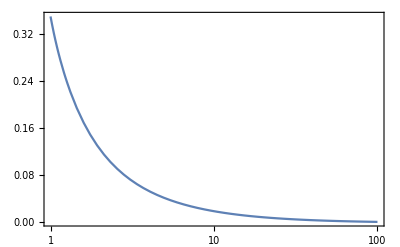
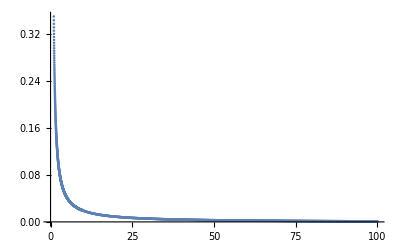

{0.927036,0.73443}

```mathematica
ScalarProfile[0.35,0.272962040068167,3]
{M,Qτ+Qξ}
```

```mathematica
IntOut[0.7,0.7,0.27,2]
```

-0.0556965

```mathematica
ShootingAlpha[0.7,2,0.27]
```

0.264628

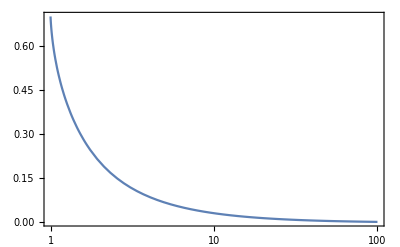
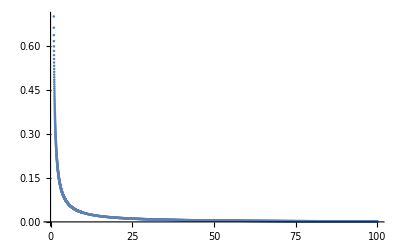

{0.97382+0.0000180902 ⅈ,1.21107+0.000635169 ⅈ}

```mathematica
ScalarProfile[0.7,0.2646275466068468,2]
{M,Qτ+Qξ}
```

```mathematica
IntOut[0.2,0.28,5]
```

0.000661968

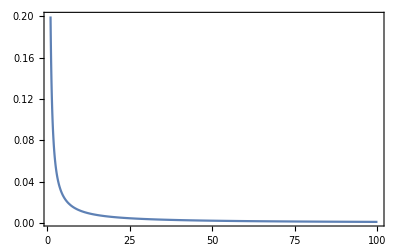

```mathematica
Plot[Re[τ[r]]/.SOLOUT,{r,rInit,100}]
```

```mathematica
ShootingAlpha[0.2,5,0.28]
```

0.280857

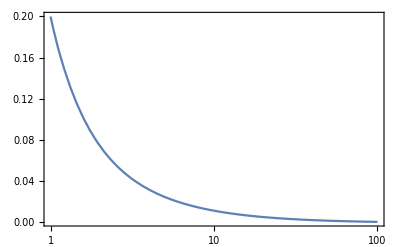
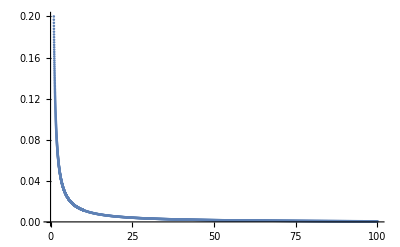

{0.915146,0.433507}

```mathematica
ScalarProfile[0.2,0.28085743505284594,5]
{M,Qτ+Qξ}
```

For same initial value, single field case has M ≂ 1.00. Here M ≂ 0.95.

### Look for M≂1 solutions for β=2 , 5

```mathematica
ShootingAlpha[0.48,0.48,2,0.24]
M
```

0.237594

1.01392

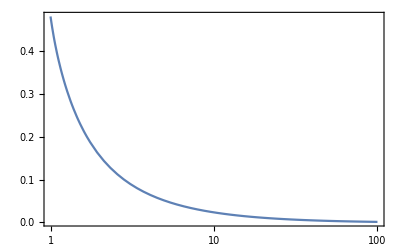
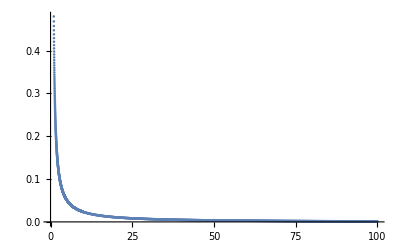

```mathematica
ScalarProfile[0.48,0.48,0.2375937900170501,2]
```

```mathematica
ShootingAlpha[0.15,0.15,5,0.24]
M
```

0.238215

1.00583

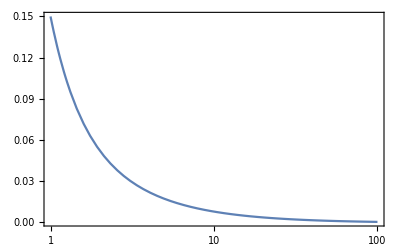
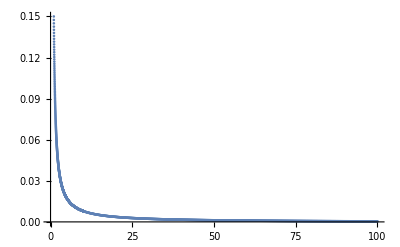

```mathematica
ScalarProfile[0.15,0.15,0.23821505936857965,5]
```

### τh = 2 ξh

```mathematica
ShootingAlpha[0.4,0.2,2,0.24]
```

0.209353

```mathematica
IntOut[0.4,0.2,0.209353,2]
```

4.57634×10^-7

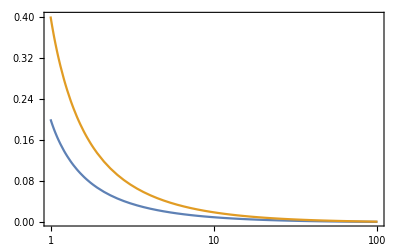

{1.08247,0.416742,0.208371}

```mathematica
LogLinearPlot[{ξ[r]/.SOLOUT,τ[r]/.SOLOUT},{r,1,100}]
{M,Qτ,Qξ}
```

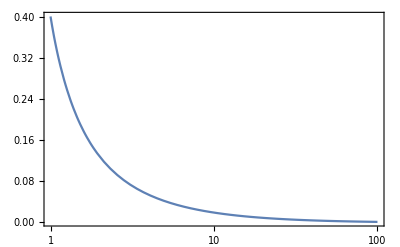

```mathematica
ScalarProfile[0.4,0.2,0.20935334747227088,2]
```

### τh = 5 ξh

```mathematica
ShootingAlpha[0.5,0.1,2,0.24]
```

0.216657

```mathematica
IntOut[0.5,0.1,0.2166570192676626,2]
```

7.96455×10^-12

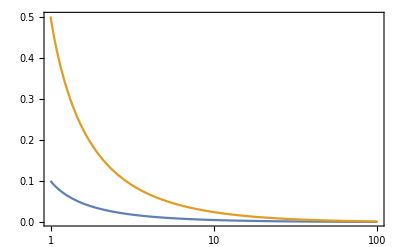

{1.06259,0.517126,0.103425}

```mathematica
LogLinearPlot[{ξ[r]/.SOLOUT,τ[r]/.SOLOUT},{r,1,100}]
{M,Qτ,Qξ}
```

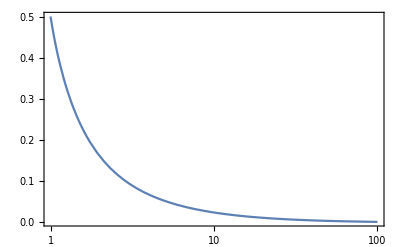
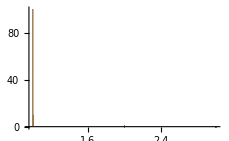

{1.08247,0.416742,0.208371}

```mathematica
ScalarProfile[0.5,0.1,0.2166570192676626,2]
```

### τh^2+ξh^2=ϕh^2

## Q-M Plots τh=ξh

### τh=ξh

#### β=0

```mathematica
ShootingAlpha[0.65,0,0.15]
```

$Aborted

```mathematica
beta0Table = Table[ScalarQM[0,phi,0.16],{phi,0.01,0.54,0.02}]
```

{{{0.181973},{1.17215,0.0105439},{1.17215,0.0105439}},{{0.181932},{1.17262,0.03162},{1.17262,0.03162}},{{0.18185},{1.17357,0.0526612},{1.17357,0.0526612}},{{0.181727},{1.17499,0.0736438},{1.17499,0.0736438}},{{0.181563},{1.17689,0.0945437},{1.17689,0.0945437}},{{0.181358},{1.17925,0.115336},{1.17925,0.115336}},{{0.181112},{1.18209,0.135996},{1.18209,0.135996}},{{0.180826},{1.18541,0.156495},{1.18541,0.156495}},{{0.180499},{1.18919,0.176806},{1.18919,0.176806}},{{0.180132},{1.19344,0.196898},{1.19344,0.196898}},{{0.179725},{1.19816,0.216738},{1.19816,0.216738}},{{0.179279},{1.20335,0.236291},{1.20335,0.236291}},{{0.178795},{1.209,0.255514},{1.209,0.255514}},{{0.178272},{1.21511,0.274363},{1.21511,0.274363}},{{0.177713},{1.22168,0.292783},{1.22168,0.292783}},{{0.177119},{1.22869,0.310708},{1.22869,0.310708}},{{0.176494},{1.23615,0.328057},{1.23615,0.328057}},{{0.175841},{1.24401,0.34472},{1.24401,0.34472}},{{0.175171},{1.25227,0.360542},{1.25227,0.360542}},{{0.174503},{1.26084,0.375262},{1.26084,0.375262}},{{0.173903},{1.26954,0.388289},{1.26954,0.388289}},{{0.173538},{1.27756+0.0000341006 ⅈ,0.398001+0.00144899 ⅈ},{1.27756+0.0000341006 ⅈ,0.398001+0.00144899 ⅈ}},{{0.172748},{1.2874+0.000276184 ⅈ,0.407398+0.00573989 ⅈ},{1.2874+0.000276184 ⅈ,0.407398+0.00573989 ⅈ}},{{0.171576},{1.2989+0.000608514 ⅈ,0.417364+0.0118013 ⅈ},{1.2989+0.000608514 ⅈ,0.417364+0.0118013 ⅈ}},{{0.170143},{1.31166+0.000960704 ⅈ,0.428012+0.0191709 ⅈ},{1.31166+0.000960704 ⅈ,0.428012+0.0191709 ⅈ}},{{0.16854},{1.32532+0.00128298 ⅈ,0.439355+0.0275728 ⅈ},{1.32532+0.00128298 ⅈ,0.439355+0.0275728 ⅈ}},{{0.166831},{1.33968+0.0015275 ⅈ,0.451377+0.0368243 ⅈ},{1.33968+0.0015275 ⅈ,0.451377+0.0368243 ⅈ}}}

{{1.17215,0.0105439},{1.17262,0.03162},{1.17357,0.0526612},{1.17499,0.0736438},{1.17689,0.0945437},{1.17925,0.115336},{1.18209,0.135996},{1.18541,0.156495},{1.18919,0.176806},{1.19344,0.196898},{1.19816,0.216738},{1.20335,0.236291},{1.209,0.255514},{1.21511,0.274363},{1.22168,0.292783},{1.22869,0.310708},{1.23615,0.328057},{1.24401,0.34472},{1.25227,0.360542},{1.26084,0.375262},{1.26954,0.388289},{1.27756+0.0000341006 ⅈ,0.398001+0.00144899 ⅈ},{1.2874+0.000276184 ⅈ,0.407398+0.00573989 ⅈ},{1.2989+0.000608514 ⅈ,0.417364+0.0118013 ⅈ},{1.31166+0.000960704 ⅈ,0.428012+0.0191709 ⅈ},{1.32532+0.00128298 ⅈ,0.439355+0.0275728 ⅈ},{1.33968+0.0015275 ⅈ,0.451377+0.0368243 ⅈ}}

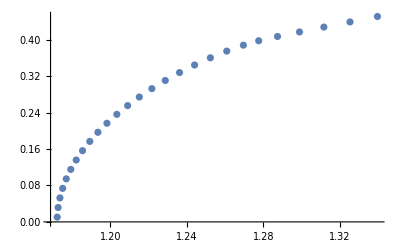

```mathematica
beta0Double = beta0Table[[;;,2]]
ListPlot[Re[beta0Double]]
```

#### β=1

```mathematica
ShootingAlpha[0.55,1,0.18]
```

0.181153

```mathematica
beta1Table = Table[ScalarQM[1,phi,0.18],{phi,0.01,0.6,0.02}]
```

{{{0.181979},{1.1721,0.010544},{1.1721,0.010544}},{{0.181986},{1.17218,0.0316238},{1.17218,0.0316238}},{{0.181999},{1.17236,0.0526785},{1.17236,0.0526785}},{{0.182018},{1.17262,0.0736916},{1.17262,0.0736916}},{{0.182043},{1.17297,0.094646},{1.17297,0.094646}},{{0.182073},{1.17341,0.115525},{1.17341,0.115525}},{{0.182108},{1.17395,0.13631},{1.17395,0.13631}},{{0.182145},{1.17458,0.156984},{1.17458,0.156984}},{{0.182186},{1.17532,0.177529},{1.17532,0.177529}},{{0.182227},{1.17617,0.197926},{1.17617,0.197926}},{{0.182268},{1.17712,0.218154},{1.17712,0.218154}},{{0.182307},{1.1782,0.238194},{1.1782,0.238194}},{{0.182344},{1.17939,0.258025},{1.17939,0.258025}},{{0.182375},{1.18072,0.277624},{1.18072,0.277624}},{{0.182399},{1.18218,0.296968},{1.18218,0.296968}},{{0.182414},{1.18378,0.316031},{1.18378,0.316031}},{{0.182418},{1.18553,0.334788},{1.18553,0.334788}},{{0.18241},{1.18744,0.353208},{1.18744,0.353208}},{{0.182385},{1.18951,0.371262},{1.18951,0.371262}},{{0.182343},{1.19175,0.388914},{1.19175,0.388914}},{{0.182281},{1.19417,0.406126},{1.19417,0.406126}},{{0.182197},{1.19678,0.422853},{1.19678,0.422853}},{{0.182088},{1.19957,0.439046},{1.19957,0.439046}},{{0.181952},{1.20255,0.454641},{1.20255,0.454641}},{{0.181789},{1.20574,0.469562},{1.20574,0.469562}},{{0.181598},{1.20912,0.483705},{1.20912,0.483705}},{{0.181383},{1.21268,0.496914},{1.21268,0.496914}},{{0.181153},{1.21639,0.508913},{1.21639,0.508913}},{{0.180988},{1.22-0.0000130482 ⅈ,0.518736+0.000109833 ⅈ},{1.22-0.0000130482 ⅈ,0.518736+0.000109833 ⅈ}},{{0.180759},{1.22388-0.000060515 ⅈ,0.526563+0.00214191 ⅈ},{1.22388-0.000060515 ⅈ,0.526563+0.00214191 ⅈ}}}

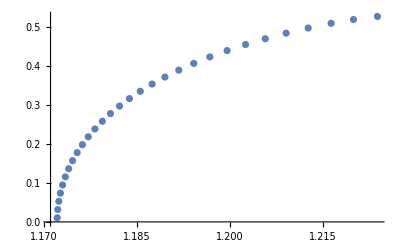

```mathematica
beta1Double = beta1Table[[;;,2]];
ListPlot[Re[beta1Double]]
```

#### β =2

```mathematica
ShootingAlpha[0.5,2,0.2]
```

0.241016

```mathematica
beta2Table = Table[ScalarQM[2,phi,0.24],{phi,0.01,0.7,0.02}]
```

{{{0.182008},{1.17198,0.0105444},{1.17198,0.0105444}},{{0.182243},{1.17109,0.0316331},{1.17109,0.0316331}},{{0.182713},{1.16934,0.0527214},{1.16934,0.0527214}},{{0.183416},{1.16673,0.0738082},{1.16673,0.0738082}},{{0.18435},{1.16328,0.0948907},{1.16328,0.0948907}},{{0.185512},{1.15905,0.115964},{1.15905,0.115964}},{{0.186899},{1.15406,0.137022},{1.15406,0.137022}},{{0.188506},{1.14837,0.158055},{1.14837,0.158055}},{{0.190326},{1.14203,0.17905},{1.14203,0.17905}},{{0.192355},{1.13511,0.199991},{1.13511,0.199991}},{{0.194583},{1.12767,0.22086},{1.12767,0.22086}},{{0.197003},{1.11979,0.241635},{1.11979,0.241635}},{{0.199604},{1.11153,0.262291},{1.11153,0.262291}},{{0.202374},{1.10297,0.282799},{1.10297,0.282799}},{{0.205301},{1.09419,0.30313},{1.09419,0.30313}},{{0.208371},{1.08527,0.323248},{1.08527,0.323248}},{{0.211568},{1.07628,0.343117},{1.07628,0.343117}},{{0.214874},{1.0673,0.362699},{1.0673,0.362699}},{{0.218272},{1.0584,0.381954},{1.0584,0.381954}},{{0.22174},{1.04963,0.400836},{1.04963,0.400836}},{{0.225256},{1.04108,0.419302},{1.04108,0.419302}},{{0.228798},{1.03284,0.437305},{1.03284,0.437305}},{{0.23234},{1.02496,0.454795},{1.02496,0.454795}},{{0.235855},{1.01748,0.471722},{1.01748,0.471722}},{{0.239315},{1.01047,0.488034},{1.01047,0.488034}},{{0.242692},{1.00397,0.503677},{1.00397,0.503677}},{{0.245955},{0.998026,0.518595},{0.998026,0.518595}},{{0.249073},{0.992677,0.532731},{0.992677,0.532731}},{{0.252014},{0.987955,0.546024},{0.987955,0.546024}},{{0.254747},{0.983885,0.558409},{0.983885,0.558409}},{{0.257241},{0.980489,0.569816},{0.980489,0.569816}},{{0.259464},{0.977779,0.580163},{0.977779,0.580163}},{{0.261385},{0.975746,0.589348},{0.975746,0.589348}},{{0.262973},{0.974455,0.597218},{0.974455,0.597218}},{{0.264188},{0.973835,0.603432},{0.973835,0.603432}}}

```mathematica
beta2Double = beta2Table[[;;,2]]
```

{{1.17198,0.0105444},{1.17109,0.0316331},{1.16934,0.0527214},{1.16673,0.0738082},{1.16328,0.0948907},{1.15905,0.115964},{1.15406,0.137022},{1.14837,0.158055},{1.14203,0.17905},{1.13511,0.199991},{1.12767,0.22086},{1.11979,0.241635},{1.11153,0.262291},{1.10297,0.282799},{1.09419,0.30313},{1.08527,0.323248},{1.07628,0.343117},{1.0673,0.362699},{1.0584,0.381954},{1.04963,0.400836},{1.04108,0.419302},{1.03284,0.437305},{1.02496,0.454795},{1.01748,0.471722},{1.01047,0.488034},{1.00397,0.503677},{0.998026,0.518595},{0.992677,0.532731},{0.987955,0.546024},{0.983885,0.558409},{0.980489,0.569816},{0.977779,0.580163},{0.975746,0.589348},{0.974455,0.597218},{0.973835,0.603432}}

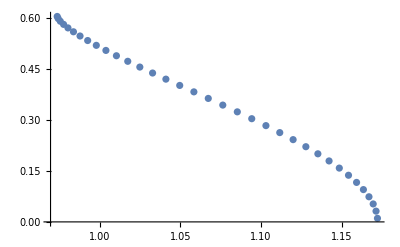

```mathematica
ListPlot[beta2Double]
```

#### β=5

```mathematica
ShootingAlpha[0.2,5,0.24]
```

0.280857

```mathematica
beta5Table = Table[ScalarQM[5,phi,0.28],{phi,0.01,0.3,0.02}]
```

{{{0.182229},{1.17118,0.0105467},{1.17118,0.0105467}},{{0.184238},{1.16396,0.0316932},{1.16396,0.0316932}},{{0.188257},{1.14986,0.0529866},{1.14986,0.0529866}},{{0.194286},{1.12954,0.0744854},{1.12954,0.0744854}},{{0.202321},{1.1039,0.0962027},{1.1039,0.0962027}},{{0.212344},{1.074,0.118107},{1.074,0.118107}},{{0.224324},{1.04095,0.14013},{1.04095,0.14013}},{{0.238215},{1.00583,0.162182},{1.00583,0.162182}},{{0.253956},{0.969637,0.18416},{0.969637,0.18416}},{{0.271468},{0.933215,0.205957},{0.933215,0.205957}},{{0.290651},{0.897274,0.227465},{0.897274,0.227465}},{{0.311387},{0.862379,0.248581},{0.862379,0.248581}},{{0.333528},{0.828968,0.269202},{0.828968,0.269202}},{{0.356898},{0.797373,0.289226},{0.797373,0.289226}},{{0.381285},{0.767837,0.30855},{0.767837,0.30855}}}

```mathematica
beta5Double=beta5Table[[;;,2]]
```

{{1.17118,0.0105467},{1.16396,0.0316932},{1.14986,0.0529866},{1.12954,0.0744854},{1.1039,0.0962027},{1.074,0.118107},{1.04095,0.14013},{1.00583,0.162182},{0.969637,0.18416},{0.933215,0.205957},{0.897274,0.227465},{0.862379,0.248581},{0.828968,0.269202},{0.797373,0.289226},{0.767837,0.30855}}

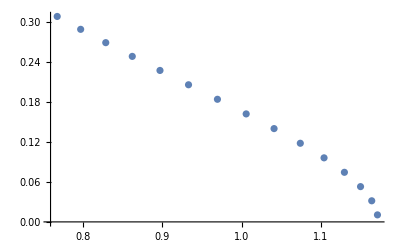

```mathematica
ListPlot[beta5Double]
```

```mathematica
Export["Plots/Doublebeta0.txt",beta0Double,"Table"]
Export["Plots/Doublebeta1.txt",beta1Double,"Table"]
Export["Plots/Doublebeta2.txt",beta2Double,"Table"]
Export["Plots/Doublebeta5.txt",beta5Double,"Table"]
```

Plots/Doublebeta0.txt

Plots/Doublebeta1.txt

Plots/Doublebeta2.txt

Plots/Doublebeta5.txt

### τh^2 + ξh^2=ϕh^2 and β=3

```mathematica
θ=π/3;
S=ScalarQM[3,0.25Cos[θ],0.25 Sin[θ],0.2];
√(S[[2,2]]^2+S[[3,2]]^2)
```

0.266166

```mathematica
θ=π/6;
S=ScalarQM[3,0.25Cos[θ],0.25 Sin[θ],0.2];
√(S[[2,2]]^2+S[[3,2]]^2)
```

0.266166

```mathematica
θ=π/4;
S=ScalarQM[3,0.25Cos[θ],0.25 Sin[θ],0.2];
√(S[[2,2]]^2+S[[3,2]]^2)
```

0.266166

```mathematica
θ=π/7;
S=ScalarQM[3,0.25Cos[θ],0.25 Sin[θ],0.2];
√(S[[2,2]]^2+S[[3,2]]^2)
```

0.266166

```mathematica
S=ScalarQM[3,0.5,0.25,0.2];
{S[[2,1]],√(S[[2,2]]^2+S[[3,2]]^2)}
```

{0.889576,0.578278}

```mathematica
NormCharge[θ_,β_,ϕc_,guess_]:=(
S =ScalarQM[β,ϕc Cos[θ],ϕc Sin[θ],guess];
{S[[2,1]],√(S[[2,2]]^2+S[[3,2]]^2)}
);
```

```mathematica
NormChargeRatio[R_,β_,ϕc_,guess_]:=(
S =ScalarQM[β,ϕc,R ϕc,guess];
{S[[2,1]],√(S[[2,2]]^2+S[[3,2]]^2)}
);
```

```mathematica
NormCharge[π/3,2,0.5,0.24]
```

{1.06571,0.517808}

```mathematica
θ=π/3;Beta2=Table[NormCharge[π/3,2,phi,0.24],{phi,0.01,1.05,0.05}]
```

{{1.17203,0.0105444},{1.1701,0.063266},{1.16548,0.115982},{1.15831,0.168671},{1.14882,0.221283},{1.1373,0.27373},{1.1241,0.325882},{1.1096,0.377566},{1.09423,0.428567},{1.07841,0.478629},{1.06255,0.527461},{1.04705,0.574741},{1.0323,0.620117},{1.01869,0.663212},{1.00649,0.703626},{0.995977,0.740936},{0.987355,0.774686},{0.98078,0.80438},{0.976328,0.829413},{0.974098,0.848813},{0.974051+0.000323448 ⅈ,0.860128+0.00314705 ⅈ}}

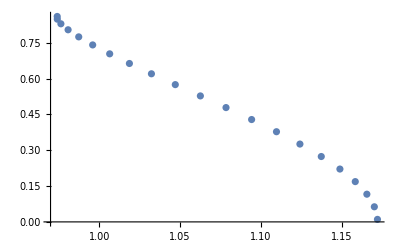

```mathematica
ListPlot[Re[%]]
```

```mathematica
Beta2A=Table[NormChargeRatio[2,2,phi,0.24],{phi,0.01,0.8,0.05}]
```

$Aborted

## Q-M Symmetry

Fix ϕh, compare with τh^2+ξh^2=ϕh^2

```mathematica
ScalarQM[2,0.25,0,0.2]
```

{{0.190991},{1.13975,0.263259},{1.13975,0.}}

```mathematica
ϕP=0.25;
θ=π/6;
ScalarQM[2,ϕP × Cos[θ],ϕP × Sin[θ],0.19]
√(Qξ^2+Qτ^2)
```

{{0.190991},{1.13975,0.227989},{1.13975,0.131629}}

0.263259

Explore the symmetry

(τ_h
ξ_h)→ (Cos[θ] | -Sin[θ]
Sin[θ] | Cos[θ])(τ_h
ξ_h).

```mathematica
ScalarQM[2,0.25,0.35,0.207]
√(Qξ^2+Qτ^2)
```

{{0.207457},{1.0879,0.260881},{1.0879,0.365233}}

0.448836

```mathematica
θ=π/8;
τI = 0.25;
ξI = 0.35;
ScalarQM[2,(τI*Cos[θ]-ξI*Sin[θ]),(τI*Sin[θ]+ξI*Cos[θ]),0.207]
√(Qξ^2+Qτ^2)
```

{{0.207457},{1.0879,0.101254},{1.0879,0.437266}}

0.448836

# Black Holes Scalarization - Complex Field R&I

## Generalise results for BH scalarization to two degrees of freedom.

## Field Equations

### Call in the Coordinate-Dep. Tensor package, define coordinates and metric

```mathematica
<<xAct`xCoba`;
<<xAct`TexAct`;
DefManifold[MC,4,IndexRange[a,n]]
DefChart[sspher,MC,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Purple]

DefScalarFunction[A]
DefScalarFunction[B]
DefScalarFunction[F]
DefScalarFunction[X]
DefScalarFunction[T]
DefConstantSymbol[α]
DefConstantSymbol[β]
DefConstantSymbol[κ]
DefConstantSymbol[η]

met=CTensor[DiagonalMatrix[{- A[r[]], (B[r[]])^-1,r[]^2,r[]^2Sin[θ[]]^2}],{-sspher,-sspher}];
SetCMetric[met,sspher,SignatureOfMetric->{3,1,0}];
CD=CovDOfMetric[met];
MetricCompute[met,sspher,All,Parallelize->True];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.3, {2021,10,28}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold MC.

** DefVBundle: Defining vbundle TangentMC.

** DefChart: Defining chart sspher.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping sspher.

** DefMapping: Defining inverse mapping isspher.

** DefTensor: Defining mapping differential tensor disspher[-a,issphera].

** DefTensor: Defining mapping differential tensor dsspher[-a,ssphera].

** DefBasis: Defining basis sspher. Coordinated basis.

** DefCovD: Defining parallel derivative PDsspher[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDsspher[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDsspher[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDsspher[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDsspher[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpsspher[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownsspher[-a,-b,-c,-d].

** DefScalarFunction: Defining scalar function A.

** DefScalarFunction: Defining scalar function B.

** DefScalarFunction: Defining scalar function F.

** DefScalarFunction: Defining scalar function X.

** DefScalarFunction: Defining scalar function T.

** DefConstantSymbol: Defining constant symbol α.

** DefConstantSymbol: Defining constant symbol β.

** DefConstantSymbol: Defining constant symbol κ.

** DefConstantSymbol: Defining constant symbol η.

### Define all the tensors

ℒ = R-1/2∇_μ τ∇_ν τ-(β R/2-α 𝒢)τ^2/2-1/2∇_μ ξ∇_ν ξ-(β R/2-α 𝒢)ξ^2/2;
Line Element: ⅆ s^2=-A[r]ⅆ t^2+(ⅆ r^2)/B[r]+r^2 ⅆ Ω^2 ;
The Einstein Tensor: G_ab;
Effective Mass Squared for Field Equation : m_eff^2=β/2 R-α𝒢, 𝒢 the Gauss Bonnet Scalar;
The Stress-Energy tensor :(T^ϕ)_μν+(T^α)_μν+ (T^β)_μν, with :
				(T^ϕ)_μν=∇_μ ϕ∇_ν ϕ-1/2 g_μν∇_α ϕ∇^α ϕ , (T^α)_μν=-α/g g_(μ(ρ)g_(σ)ν)ϵ^κραβ ϵ^σγλτ R_λταβ∇_γ ∇_κ ϕ^2, (T^β)_μν= 1/2 β(G_μν-∇_μ ∇_ν +g_μν∇_γ ∇^γ)ϕ^2.

WARNING: Define tensors without “:=”, it does not work properly otherwise!!!

```mathematica
G[a_,b_]=Einstein[CD][a,b];
𝒢 = ((RicciScalar[CD][])^2-4Ricci[CD][-a,-b]Ricci[CD][a,b]+Riemann[CD][a,b,c,d]Riemann[CD][-a,-b,-c,-d])//ContractBasis;
meffSqrd = β/2 RicciScalar[CD][]-α((RicciScalar[CD][])^2-4Ricci[CD][-a,-b]Ricci[CD][a,b]+Riemann[CD][a,b,c,d]Riemann[CD][-a,-b,-c,-d])//ContractBasis;
TPhi[a_,b_]=
(CD[a]@F[r[]]CD[b]@F[r[]]-1/2 met[a,b]CD[-c]@F[r[]]CD[c]@F[r[]]	
)//ContractBasis;
TBeta[a_,b_] =β(G[a,b](F[r[]])^2/2-CD[a]@CD[b]@((F[r[]])^2/2)+met[a,b]CD[-c]@CD[c]@((F[r[]])^2/2))//ContractBasis;
TAlphaEps[a_,b_] =-1/1 α (
2Symmetrize[met[a,-c]met[-d,b],{c,d}]epsilon[met][e,c,f,g]epsilon[met][d,h,i,l]Riemann[CD][-i,-l,-f,-g]CD[-h]@CD[-e]@((F[r[]])^2/2)
)//ContractBasis;
SETensor[a_,b_]=TAlphaEps[a,b]+TBeta[a,b]+TPhi[a,b];

Trasfξ = {F[r[]]->X[r[]],F'[r[]]->X'[r[]],F''[r[]]->X''[r[]]};
Trasfτ = {F[r[]]->T[r[]],F'[r[]]->T'[r[]],F''[r[]]->T''[r[]]};
TrasfFinal = {X[r]->ξ[r],X'[r]->ξ'[r],X''[r]->ξ''[r],
			T[r]->τ[r],T'[r]->τ'[r],T''[r]->τ''[r]};
```

## Field Equations

G_μν=κT_μν     with   T_μν=((T^ϕ)_μν+(T^α)_μν+(T^β)_μν)^τ+((T^ϕ)_μν+(T^α)_μν+(T^β)_μν)^ξ
□ϕ = m_eff^2 ϕ

```mathematica
TauEq =CD[-a]@CD[a]@T[r[]]-meffSqrd (T[r[]]);
XiEq =CD[-a]@CD[a]@X[r[]]-meffSqrd X[r[]];
ttEq=(G[{0,sspher},{0,-sspher}]
-(κ SETensor[{0,sspher},{0,-sspher}]/.Trasfξ)
-(κ SETensor[{0,sspher},{0,-sspher}]/.Trasfτ));
rrEq=(G[{1,sspher},{1,-sspher}]
-κ( SETensor[{1,sspher},{1,-sspher}]/.Trasfξ)
-κ( SETensor[{1,sspher},{1,-sspher}]/.Trasfτ));
θθEq=(G[{2,sspher},{2,-sspher}]
-κ( SETensor[{2,sspher},{2,-sspher}]/.Trasfξ)
-κ (SETensor[{2,sspher},{2,-sspher}]/.Trasfτ));
```

#### Final expression for Eq. of Motion to use in the Numerical Integrator

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ]
FinalττEq = TauEq//Expand /.{r[]->r}/.TrasfFinal;
FinalξξEq = XiEq//Expand /.{r[]->r}/.TrasfFinal;
FinalttEq = ttEq//Expand /.{r[]->r}/.TrasfFinal;
FinalrrEq = rrEq//Expand /.{r[]->r}/.TrasfFinal;
FinalθθEq = θθEq//Expand /.{r[]->r}/.TrasfFinal;
GaussBonnet = 𝒢//Expand /.{r[]->r}/.TrasfFinal;

FieldEqs = {FinalttEq,FinalrrEq,FinalθθEq,FinalττEq,FinalξξEq}/.{r[]->r,η->1,κ->1/2}/.TrasfFinal;
MatrixForm[FieldEqs]
```

```mathematica
FieldEqs =({{-1/r^2+B[r]/r^2+(β ξ[r]^2)/(4 r^2)-(β B[r] ξ[r]^2)/(4 r^2)+(β τ[r]^2)/(4 r^2)-(β B[r] τ[r]^2)/(4 r^2)+B'[r]/r-(β ξ[r]^2 B'[r])/(4 r)-(β τ[r]^2 B'[r])/(4 r)-(β B[r] ξ[r] ξ'[r])/r+(2 α ξ[r] B'[r] ξ'[r])/r^2-1/4 β ξ[r] B'[r] ξ'[r]-(6 α B[r] ξ[r] B'[r] ξ'[r])/r^2+1/4 B[r] ξ'[r]^2+(4 α B[r] ξ'[r]^2)/r^2-1/2 β B[r] ξ'[r]^2-(4 α B[r]^2 ξ'[r]^2)/r^2-(β B[r] τ[r] τ'[r])/r+(2 α τ[r] B'[r] τ'[r])/r^2-1/4 β τ[r] B'[r] τ'[r]-(6 α B[r] τ[r] B'[r] τ'[r])/r^2+1/4 B[r] τ'[r]^2+(4 α B[r] τ'[r]^2)/r^2-1/2 β B[r] τ'[r]^2-(4 α B[r]^2 τ'[r]^2)/r^2+(4 α B[r] ξ[r] ξ''[r])/r^2-1/2 β B[r] ξ[r] ξ''[r]-(4 α B[r]^2 ξ[r] ξ''[r])/r^2+(4 α B[r] τ[r] τ''[r])/r^2-1/2 β B[r] τ[r] τ''[r]-(4 α B[r]^2 τ[r] τ''[r])/r^2}, {-1/r^2+B[r]/r^2+(β ξ[r]^2)/(4 r^2)-(β B[r] ξ[r]^2)/(4 r^2)+(β τ[r]^2)/(4 r^2)-(β B[r] τ[r]^2)/(4 r^2)+(B[r] A'[r])/(r A[r])-(β B[r] ξ[r]^2 A'[r])/(4 r A[r])-(β B[r] τ[r]^2 A'[r])/(4 r A[r])-(β B[r] ξ[r] ξ'[r])/r+(2 α B[r] ξ[r] A'[r] ξ'[r])/(r^2 A[r])-(β B[r] ξ[r] A'[r] ξ'[r])/(4 A[r])-(6 α B[r]^2 ξ[r] A'[r] ξ'[r])/(r^2 A[r])-1/4 B[r] ξ'[r]^2-(β B[r] τ[r] τ'[r])/r+(2 α B[r] τ[r] A'[r] τ'[r])/(r^2 A[r])-(β B[r] τ[r] A'[r] τ'[r])/(4 A[r])-(6 α B[r]^2 τ[r] A'[r] τ'[r])/(r^2 A[r])-1/4 B[r] τ'[r]^2}, {(B[r] A'[r])/(2 r A[r])-(β B[r] ξ[r]^2 A'[r])/(8 r A[r])-(β B[r] τ[r]^2 A'[r])/(8 r A[r])-(B[r] A'[r]^2)/(4 A[r]^2)+(β B[r] ξ[r]^2 A'[r]^2)/(16 A[r]^2)+(β B[r] τ[r]^2 A'[r]^2)/(16 A[r]^2)+B'[r]/(2 r)-(β ξ[r]^2 B'[r])/(8 r)-(β τ[r]^2 B'[r])/(8 r)+(A'[r] B'[r])/(4 A[r])-(β ξ[r]^2 A'[r] B'[r])/(16 A[r])-(β τ[r]^2 A'[r] B'[r])/(16 A[r])-(β B[r] ξ[r] ξ'[r])/(2 r)-(β B[r] ξ[r] A'[r] ξ'[r])/(4 A[r])+(α B[r]^2 ξ[r] A'[r]^2 ξ'[r])/(r A[r]^2)-1/4 β ξ[r] B'[r] ξ'[r]-(3 α B[r] ξ[r] A'[r] B'[r] ξ'[r])/(r A[r])+1/4 B[r] ξ'[r]^2-1/2 β B[r] ξ'[r]^2-(2 α B[r]^2 A'[r] ξ'[r]^2)/(r A[r])-(β B[r] τ[r] τ'[r])/(2 r)-(β B[r] τ[r] A'[r] τ'[r])/(4 A[r])+(α B[r]^2 τ[r] A'[r]^2 τ'[r])/(r A[r]^2)-1/4 β τ[r] B'[r] τ'[r]-(3 α B[r] τ[r] A'[r] B'[r] τ'[r])/(r A[r])+1/4 B[r] τ'[r]^2-1/2 β B[r] τ'[r]^2-(2 α B[r]^2 A'[r] τ'[r]^2)/(r A[r])+(B[r] A''[r])/(2 A[r])-(β B[r] ξ[r]^2 A''[r])/(8 A[r])-(β B[r] τ[r]^2 A''[r])/(8 A[r])-(2 α B[r]^2 ξ[r] ξ'[r] A''[r])/(r A[r])-(2 α B[r]^2 τ[r] τ'[r] A''[r])/(r A[r])-1/2 β B[r] ξ[r] ξ''[r]-(2 α B[r]^2 ξ[r] A'[r] ξ''[r])/(r A[r])-1/2 β B[r] τ[r] τ''[r]-(2 α B[r]^2 τ[r] A'[r] τ''[r])/(r A[r])}, {-(β τ[r])/r^2+(β B[r] τ[r])/r^2+(β B[r] τ[r] A'[r])/(r A[r])+(2 α B[r] τ[r] A'[r]^2)/(r^2 A[r]^2)-(β B[r] τ[r] A'[r]^2)/(4 A[r]^2)-(2 α B[r]^2 τ[r] A'[r]^2)/(r^2 A[r]^2)+(β τ[r] B'[r])/r-(2 α τ[r] A'[r] B'[r])/(r^2 A[r])+(β τ[r] A'[r] B'[r])/(4 A[r])+(6 α B[r] τ[r] A'[r] B'[r])/(r^2 A[r])+(2 B[r] τ'[r])/r+(B[r] A'[r] τ'[r])/(2 A[r])+1/2 B'[r] τ'[r]-(4 α B[r] τ[r] A''[r])/(r^2 A[r])+(β B[r] τ[r] A''[r])/(2 A[r])+(4 α B[r]^2 τ[r] A''[r])/(r^2 A[r])+B[r] τ''[r]}, {-(β ξ[r])/r^2+(β B[r] ξ[r])/r^2+(β B[r] ξ[r] A'[r])/(r A[r])+(2 α B[r] ξ[r] A'[r]^2)/(r^2 A[r]^2)-(β B[r] ξ[r] A'[r]^2)/(4 A[r]^2)-(2 α B[r]^2 ξ[r] A'[r]^2)/(r^2 A[r]^2)+(β ξ[r] B'[r])/r-(2 α ξ[r] A'[r] B'[r])/(r^2 A[r])+(β ξ[r] A'[r] B'[r])/(4 A[r])+(6 α B[r] ξ[r] A'[r] B'[r])/(r^2 A[r])+(2 B[r] ξ'[r])/r+(B[r] A'[r] ξ'[r])/(2 A[r])+1/2 B'[r] ξ'[r]-(4 α B[r] ξ[r] A''[r])/(r^2 A[r])+(β B[r] ξ[r] A''[r])/(2 A[r])+(4 α B[r]^2 ξ[r] A''[r])/(r^2 A[r])+B[r] ξ''[r]}});
```

Get the system of ODE from the field equations and express it re-naming the metric functions as follows

ⅆ s^2=-x[r]ⅆ t^2+(ⅆ r^2)/y[r]+r^2 ⅆ Ω^2

```mathematica
AlgebSystem=Solve[(FieldEqs)==0,{ξ''[r],τ''[r],A'[r],B'[r],A''[r]}][[1]][[1;;4]]/.{Rule->Subtract}/.{A[r]->x[r],B[r]->y[r],A'[r]->x'[r],B'[r]->y'[r],A''[r]->x''[r],B''[r]->y''[r]};
```

## Boundary Conditions

### Perturbative Solution @ Horizon

We will start integrating from the event horizon. Here the functions diverge (A,B) or vanish (σ,ρ). We have to implement appropriate boundary conditions solving the equations in perturbation theory.  
First, we move to the σ-ρ expression for the metric and solve the algebraic system for the relevant functions.

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y,ξ,τ]
ODEsysytem = FieldEqs/.Trasf//Expand;
```

```mathematica
HorizonSystem = AlgebSystem
```

{-((-3072 r^3 α ξ[r]+6144 r^3 α y[r] ξ[r]-3072 r^3 α y[r]^2 ξ[r]+3072 r^3 α β ξ[r]^3-6144 r^3 α β y[r] ξ[r]^3+3511+64 r^7 α^2 β^2 y[r]^3 ξ[r] τ[r]^2 τ'[r]^6+36864 r^3 α^4 y[r]^4 ξ[r] τ[r]^2 τ'[r]^6-4608 r^5 α^3 β y[r]^4 ξ[r] τ[r]^2 τ'[r]^6-36864 r^3 α^4 y[r]^5 ξ[r] τ[r]^2 τ'[r]^6)/(256 r^7 y[r]-12288 r^3 α^2 y[r] ξ[r]^2-256 r^7 β y[r] ξ[r]^2+192 r^7 β^2 y[r] ξ[r]^2+1338+192 r^7 α^2 β^2 y[r]^3 τ[r]^4 τ'[r]^4-135168 r^3 α^4 y[r]^4 τ[r]^4 τ'[r]^4+16896 r^5 α^3 β y[r]^4 τ[r]^4 τ'[r]^4+184320 r^3 α^4 y[r]^5 τ[r]^4 τ'[r]^4))+ξ''[r],-1/1+τ''[r],x'[r]+1/1,y'[r]+(r (1))/1}
 |  |  |  |

Then, let’s expand them near the horizon.

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
x[r_]:=∑_(i=1)^3 Subscript[a, i](r-1)^i; (*Define all the functions as a power series; n.b. horizon at r=1*)
y[r_] :=∑_(i=1)^3 Subscript[b, i](r-1)^i;(* these definitions will be inserted in the system*)
τ[r_]:=∑_(i=0)^3 Subscript[t, i](r-1)^i;
ξ[r_]:=∑_(i=0)^3 Subscript[e, i](r-1)^i;
```

Hence we solve the equations order by order, getting a proper solution with free parameters the value of the scalar field and the first derivative of σ at the horizon.

```mathematica
HorEqs = Series[{HorizonSystem[[1]](r-1),HorizonSystem[[2]](r-1),HorizonSystem[[3]],HorizonSystem[[4]]},{r,1,3}];
HorEqs1 = Table[SeriesCoefficient[HorEqs[[i]],0],{i,1,3}];
(*HorEqs2 = Table[SeriesCoefficient[HorEqs[[i]],1],{i,1,3}];*)
```

```mathematica
HorEqs1 = Table[SeriesCoefficient[HorEqs[[i]],0],{i,1,4}];
```

```mathematica
HorEqs1
```

{-((-3072 α e_0+3072 α β e_0^3-1152 α β^2 e_0^5+192 α β^3 e_0^7-12 α β^4 e_0^9-256 e_1-6144 α^2 e_0^2 e_1+256 β e_0^2 e_1+425+6 β^5 e_0^2 e_1 t_0^4 t_1^2-64 α^2 β^2 e_1 t_0^6 t_1^2-1536 α^3 β^2 e_1 t_0^6 t_1^2+16 α β^3 e_1 t_0^6 t_1^2+576 α^2 β^3 e_1 t_0^6 t_1^2-β^4 e_1 t_0^6 t_1^2-72 α β^4 e_1 t_0^6 t_1^2+3 β^5 e_1 t_0^6 t_1^2)/(256 b_1-12288 α^2 b_1 e_0^2-256 β b_1 e_0^2+192 β^2 b_1 e_0^2+9216 α^2 β b_1 e_0^4+358+64 α^2 β^2 b_1 t_0^6 t_1^2+1536 α^3 β^2 b_1 t_0^6 t_1^2-16 α β^3 b_1 t_0^6 t_1^2-576 α^2 β^3 b_1 t_0^6 t_1^2+β^4 b_1 t_0^6 t_1^2+72 α β^4 b_1 t_0^6 t_1^2-3 β^5 b_1 t_0^6 t_1^2)),-1/1,a_1-1/1,b_1+1/(-16+56+3 1^3 1 t_1)}
 |  |  |  |

```mathematica
InitialConditions=Solve[(HorEqs1)==0,{Subscript[e, 1],Subscript[b, 1],Subscript[t, 1]}]//Simplify
```

```mathematica
InitialConditions={{Subscript[e, 1]->(Subscript[e, 0] (-(-4+β Subscript[e, 0]^2) (4+β (-1-24 α+3 β) Subscript[e, 0]^2) Subscript[t, 0]+2 β (-4-48 α+6 β+(1+24 α-3 β) β Subscript[e, 0]^2) Subscript[t, 0]^3+(1+24 α-3 β) β^2 Subscript[t, 0]^5-√(Subscript[t, 0]^2 (-4+β Subscript[e, 0]^2+β Subscript[t, 0]^2)^2 (16+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^4-8 (192 α^2+β-3 β^2) Subscript[t, 0]^2+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^4+2 Subscript[e, 0]^2 (-4 (192 α^2+β-3 β^2)+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^2)))))/(2 (8 α-β) Subscript[t, 0] (Subscript[e, 0]^2+Subscript[t, 0]^2) (-4+(1+24 α-3 β) β Subscript[e, 0]^2+(1+24 α-3 β) β Subscript[t, 0]^2)),Subscript[b, 1]->1/(24 α (8 α-β) Subscript[t, 0] (Subscript[e, 0]^2+Subscript[t, 0]^2) (-4+β Subscript[e, 0]^2+β Subscript[t, 0]^2))((-4+β Subscript[e, 0]^2) (4+β (-1-24 α+3 β) Subscript[e, 0]^2) Subscript[t, 0]+2 β (4+48 α-6 β+β (-1-24 α+3 β) Subscript[e, 0]^2) Subscript[t, 0]^3+β^2 (-1-24 α+3 β) Subscript[t, 0]^5+√(Subscript[t, 0]^2 (-4+β Subscript[e, 0]^2+β Subscript[t, 0]^2)^2 (16+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^4-8 (192 α^2+β-3 β^2) Subscript[t, 0]^2+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^4+2 Subscript[e, 0]^2 (-4 (192 α^2+β-3 β^2)+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^2)))),Subscript[t, 1]->-(((-4+β Subscript[e, 0]^2) (4+β (-1-24 α+3 β) Subscript[e, 0]^2) Subscript[t, 0]-2 β (-4-48 α+6 β+(1+24 α-3 β) β Subscript[e, 0]^2) Subscript[t, 0]^3-(1+24 α-3 β) β^2 Subscript[t, 0]^5+√(Subscript[t, 0]^2 (-4+β Subscript[e, 0]^2+β Subscript[t, 0]^2)^2 (16+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^4-8 (192 α^2+β-3 β^2) Subscript[t, 0]^2+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^4+2 Subscript[e, 0]^2 (-4 (192 α^2+β-3 β^2)+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^2))))/(2 (8 α-β) (Subscript[e, 0]^2+Subscript[t, 0]^2) (-4+(1+24 α-3 β) β Subscript[e, 0]^2+(1+24 α-3 β) β Subscript[t, 0]^2)))},{Subscript[e, 1]->(Subscript[e, 0] (-(-4+β Subscript[e, 0]^2) (4+β (-1-24 α+3 β) Subscript[e, 0]^2) Subscript[t, 0]+2 β (-4-48 α+6 β+(1+24 α-3 β) β Subscript[e, 0]^2) Subscript[t, 0]^3+(1+24 α-3 β) β^2 Subscript[t, 0]^5+√(Subscript[t, 0]^2 (-4+β Subscript[e, 0]^2+β Subscript[t, 0]^2)^2 (16+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^4-8 (192 α^2+β-3 β^2) Subscript[t, 0]^2+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^4+2 Subscript[e, 0]^2 (-4 (192 α^2+β-3 β^2)+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^2)))))/(2 (8 α-β) Subscript[t, 0] (Subscript[e, 0]^2+Subscript[t, 0]^2) (-4+(1+24 α-3 β) β Subscript[e, 0]^2+(1+24 α-3 β) β Subscript[t, 0]^2)),Subscript[b, 1]->1/(24 α (8 α-β) Subscript[t, 0] (Subscript[e, 0]^2+Subscript[t, 0]^2) (-4+β Subscript[e, 0]^2+β Subscript[t, 0]^2))((-4+β Subscript[e, 0]^2) (4+β (-1-24 α+3 β) Subscript[e, 0]^2) Subscript[t, 0]+2 β (4+48 α-6 β+β (-1-24 α+3 β) Subscript[e, 0]^2) Subscript[t, 0]^3+β^2 (-1-24 α+3 β) Subscript[t, 0]^5-√(Subscript[t, 0]^2 (-4+β Subscript[e, 0]^2+β Subscript[t, 0]^2)^2 (16+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^4-8 (192 α^2+β-3 β^2) Subscript[t, 0]^2+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^4+2 Subscript[e, 0]^2 (-4 (192 α^2+β-3 β^2)+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^2)))),Subscript[t, 1]->(-(-4+β Subscript[e, 0]^2) (4+β (-1-24 α+3 β) Subscript[e, 0]^2) Subscript[t, 0]+2 β (-4-48 α+6 β+(1+24 α-3 β) β Subscript[e, 0]^2) Subscript[t, 0]^3+(1+24 α-3 β) β^2 Subscript[t, 0]^5+√(Subscript[t, 0]^2 (-4+β Subscript[e, 0]^2+β Subscript[t, 0]^2)^2 (16+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[e, 0]^4-8 (192 α^2+β-3 β^2) Subscript[t, 0]^2+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^4+2 Subscript[e, 0]^2 (-4 (192 α^2+β-3 β^2)+β (9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β)) Subscript[t, 0]^2))))/(2 (8 α-β) (Subscript[e, 0]^2+Subscript[t, 0]^2) (-4+(1+24 α-3 β) β Subscript[e, 0]^2+(1+24 α-3 β) β Subscript[t, 0]^2))}};
```

```mathematica
δ=16+(9216 α^3+(1-3 β)^2 β-192 α^2 (-2+9 β))β  (Subscript[e, 0]^2+Subscript[t, 0]^2)^2-8 (192 α^2+β-3 β^2)( Subscript[t, 0]^2+Subscript[e, 0]^2);
𝓂=2 (8 α-β) (Subscript[e, 0]^2+Subscript[t, 0]^2) (-4+ β (Subscript[e, 0]^2+Subscript[t, 0]^2)+(24 α-3 β)( β Subscript[e, 0]^2+β Subscript[t, 0]^2)) /(Subscript[t, 0] (-4+β (Subscript[e, 0]^2+Subscript[t, 0]^2))) ;
𝓃=-4+β(Subscript[e, 0]^2+Subscript[t, 0]^2)+(24 α-3 β)β(Subscript[e, 0]^2+Subscript[t, 0]^2);

TauPrimeHorizon = (𝓃+√δ)/𝓂//Simplify;
XiPrimeHorizon = Subscript[e, 0]/Subscript[t, 0] TauPrimeHorizon;
yPrimeHorizon=(-β/(8 α)+(4-β( Subscript[e, 0]^2 +Subscript[t, 0]^2)-√δ)/(24 α (8 α-β) (Subscript[e, 0]^2+Subscript[t, 0]^2)));
```

```mathematica
ScalarValues[αc_,βc_] :=Reduce[{(δ/.{β->βc,Subscript[t, 0]->ϕh,Subscript[e, 0]->ϕh,α->αc})>0&&ϕh>0&&α>0},{ϕh}]//N
AlphaValues[ϕc_,βc_] :=Reduce[{(δ/.{β->βc,Subscript[t, 0]->ϕc,Subscript[e, 0]->ϕc})>0&&α>0&&ϕc>0},{α}]//N
```

```mathematica
AlphaValues[0.4,0]
ScalarValues[0.17,0]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.<α<0.180422

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

α>0.&&0.<ϕh<0.424522

### Perturbative Solution @ Infinity

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
InfSystem = AlgebSystem;
```

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
x[r_]:=1+∑_(i=1)^3 Subscript[a, i](r)^-i ;(*Define all the functions as a power series; n.b. horizon at r=1*)
y[r_] :=1+∑_(i=1)^3 Subscript[b, i](r)^-i;(* these definitions will be inserted in the system*)
τ[r_]:=∑_(i=1)^3 Subscript[t, i](r)^-i;
ξ[r_]:=∑_(i=1)^3 Subscript[e, i](r)^-i;
```

$Aborted

```mathematica
Series[InfSystem[[1]] r^4,{r,∞,2} ]
```

(b_1 e_1+2 e_2)+(-4 b_1^2 e_1+4 b_2 e_1+3 β^2 e_1^3+8 b_1 e_2+24 e_3+3 β^2 e_1 t_1^2)/(4 r)+1/(4 r^2)(4 b_1^3 e_1-8 b_1 b_2 e_1+4 b_3 e_1-8 b_1^2 e_2+8 b_2 e_2-β e_1^2 e_2+15 β^2 e_1^2 e_2+12 b_1 e_3+β e_2 t_1^2+3 β^2 e_2 t_1^2-2 β e_1 t_1 t_2+12 β^2 e_1 t_1 t_2)+O[1/r]^3

```mathematica
InfEqs = Series[{InfSystem[[2]] r^4,InfSystem[[3]] r^2,InfSystem[[4]] r^3},{r,∞,2}];
```

$Aborted

```mathematica
InfEqs = Series[{InfSystem[[1]] r^4,InfSystem[[2]] r^4,InfSystem[[3]] r^2,InfSystem[[4]] r^3},{r,∞,2}];
InfEqs1 = Table[SeriesCoefficient[InfEqs[[i]],0],{i,1,4}];
InfEqs2 = Table[SeriesCoefficient[InfEqs[[i]],1],{i,1,4}];
InfEqs3 = Table[SeriesCoefficient[InfEqs[[i]],2],{i,1,4}];
```

```mathematica
InfFirst = Solve[InfEqs1==0,{Subscript[t, 2],Subscript[e, 2],Subscript[a, 1],Subscript[b, 2]}][[1]]
InfSecond = Solve[InfEqs2==0,{Subscript[t, 3],Subscript[e, 3],Subscript[a, 2],Subscript[b, 3]}][[1]]/.InfFirst
InfThird = Solve[InfEqs3[[3]]==0,{Subscript[a, 3]}][[1]]/.InfFirst
```

{t_2→-1/2 b_1 t_1,e_2→-1/2 b_1 e_1,a_1→b_1,b_2→1/4 (e_1^2-2 β e_1^2+t_1^2-2 β t_1^2)}

{t_3→1/24 (8 b_1^2 t_1-3 β^2 e_1^2 t_1-3 β^2 t_1^3-t_1 (e_1^2-2 β e_1^2+t_1^2-2 β t_1^2)),e_3→1/24 (8 b_1^2 e_1-3 β^2 e_1^3-3 β^2 e_1 t_1^2-e_1 (e_1^2-2 β e_1^2+t_1^2-2 β t_1^2)),a_2→1/8 (2 β e_1^2+2 β t_1^2),b_3→1/8 (-b_1 e_1^2+3 β b_1 e_1^2-b_1 t_1^2+3 β b_1 t_1^2)}

{a_3→1/12 (4 a_2 b_1+4 b_3+b_1 e_1^2-3 β b_1 e_1^2+b_1 t_1^2-3 β b_1 t_1^2-b_1 (e_1^2-2 β e_1^2+t_1^2-2 β t_1^2))}

```mathematica
InfCondition = Join[InfFirst,InfSecond,InfThird];
InfSolution={x[r],y[r],τ[r],ξ[r]}//.InfCondition/.Subscript[b, 1]->-2Ms/.Subscript[t, 1]->Qτ/.Subscript[t, 0]->0/.Subscript[e, 1]->Qξ/.Subscript[e, 0]->0//Expand
```

{1+(Ms Qξ^2)/(12 r^3)+(Ms Qτ^2)/(12 r^3)-(2 Ms)/r-(Ms Qξ^2 β)/(4 r^3)-(Ms Qτ^2 β)/(4 r^3)+(Qξ^2 β)/(4 r^2)+(Qτ^2 β)/(4 r^2),1+(Ms Qξ^2)/(4 r^3)+(Ms Qτ^2)/(4 r^3)+Qξ^2/(4 r^2)+Qτ^2/(4 r^2)-(2 Ms)/r-(3 Ms Qξ^2 β)/(4 r^3)-(3 Ms Qτ^2 β)/(4 r^3)-(Qξ^2 β)/(2 r^2)-(Qτ^2 β)/(2 r^2),(4 Ms^2 Qτ)/(3 r^3)-(Qξ^2 Qτ)/(24 r^3)-Qτ^3/(24 r^3)+(Ms Qτ)/r^2+Qτ/r+(Qξ^2 Qτ β)/(12 r^3)+(Qτ^3 β)/(12 r^3)-(Qξ^2 Qτ β^2)/(8 r^3)-(Qτ^3 β^2)/(8 r^3),(4 Ms^2 Qξ)/(3 r^3)-Qξ^3/(24 r^3)-(Qξ Qτ^2)/(24 r^3)+(Ms Qξ)/r^2+Qξ/r+(Qξ^3 β)/(12 r^3)+(Qξ Qτ^2 β)/(12 r^3)-(Qξ^3 β^2)/(8 r^3)-(Qξ Qτ^2 β^2)/(8 r^3)}

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y,τ,ξ]
```

```mathematica
Solve[{1+(Ms Qξ^2)/(12 r^3)+(Ms Qτ^2)/(12 r^3)-(2 Ms)/r-(Ms Qξ^2 β)/(4 r^3)-(Ms Qτ^2 β)/(4 r^3)+(Qξ^2 β)/(4 r^2)+(Qτ^2 β)/(4 r^2),-Qτ/r^2,-Qξ/r^2}=={x[r],τ'[r],ξ'[r]},{Qξ,Qτ,Ms}]//Simplify
```

{{Qξ→-r^2 ξ'[r],Qτ→-r^2 τ'[r],Ms→(3 r (4-4 x[r]+r^2 β ξ'[r]^2+r^2 β τ'[r]^2))/(24+r^2 (-1+3 β) ξ'[r]^2+r^2 (-1+3 β) τ'[r]^2)}}

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y]
SCharge[r_] = -r^2 ϕ'[r];
BHMass[r_] = (3 r (4-4 x[r]+r^2 β (ξ'[r]^2+τ'[r]^2)))/(24+r^2 (-1+3 β) (ξ'[r]^2+τ'[r]^2));
```

## Numerical Integration - “Algebraic”

```mathematica
Clear[A,B,ϕ,λ,σ,κ,α,γ,x,y,ξ,τ]
SetOptions[NDSolve,MaxSteps->Infinity,Method->"StiffnessSwitching",AccuracyGoal->10];
SetOptions[LogLinearPlot,Frame->True,PlotRange->All];
SetOptions[Plot,Frame->True,PlotRange->All];
SetDirectory[NotebookDirectory[]]; 

rhc = 1;
δ=10^-4;
rMax=200;
```

```mathematica
IntOut[τc_?NumericQ,ξc_?NumericQ,αc_?NumericQ,βc_]:=(
rInit = rhc+δ;
Par = {r->rInit,rh->rhc,Subscript[t, 0]->τc,Subscript[e, 0]->ξc,α->αc,β->βc,ϕh->ϕc};
BOUND =
{
τ[rInit] ==  τc,
τ'[rInit] ==  TauPrimeHorizon,
ξ[rInit] ==  ξc,
ξ'[rInit] ==  XiPrimeHorizon,
x[rInit] == Subscript[a, 1](rInit-rhc),
y[rInit]==yPrimeHorizon(rInit-rhc)
}/.Par;
EQS = {AlgebSystem =={0,0,0,0}}/.{α->αc,β-> βc,η->1};
SOLOUT = NDSolve[Join[BOUND/.{Subscript[a, 1]->1},EQS],{x,y,τ,ξ},{r,rInit,rMax}][[1]];
InfRatio = (y[rMax]/x[rMax])/.SOLOUT/.{α->αc,β->βc};
SOLOUT = NDSolve[Join[BOUND/.{Subscript[a, 1]->InfRatio},EQS],{x,y,τ,ξ},{r,rInit,rMax}][[1]];
Qτ = SCharge[rMax]/(√αc)/.{ϕ'[rMax]->τ'[rMax],α->αc,β->βc,r->rMax}/.SOLOUT;
Qξ = SCharge[rMax]/(√αc)/.{ϕ'[rMax]->ξ'[rMax],α->αc,β->βc,r->rMax}/.SOLOUT;
M=BHMass[rMax]/(√αc)/.{α->αc,β->βc}/.SOLOUT;
τINF = Re[τ[rMax]]/.SOLOUT;
ξINF = Re[ξ[rMax]]/.SOLOUT;

(τINF+ξINF)/2
)

ShootingAlpha[τc_?NumericQ,ξc_?NumericQ,β_?NumericQ,guess_]:=(
Clear[f,InfPhiAlpha];
InfPhiAlpha[f_?NumericQ]:=IntOut[τc,ξc,f,β];
f/.FindRoot[IntOut[τc,ξc,f,β],{f,guess},PrecisionGoal->4]
)
ScalarProfile[τc_?NumericQ,ξc_?NumericQ,αc_,βc_]:=(
IntOut[τc,ξc,αc,βc];
Points1 = Table[{r,Re[τ[r]]/.SOLOUT,Re[ξ[r]]/.SOLOUT,
√(Re[τ[r]]^2+Re[ξ[r]]^2)/.SOLOUT,ArcTan[Re[ξ[r]]/Re[τ[r]]]/.SOLOUT},{r,rInit,10,0.01}];
Points2 = Table[{r,Re[τ[r]]/.SOLOUT,Re[ξ[r]]/.SOLOUT,
√(Re[τ[r]]^2+Re[ξ[r]]^2)/.SOLOUT,ArcTan[Re[ξ[r]]/Re[τ[r]]]/.SOLOUT},{r,10,100,0.1}];
Points = Join[Points1,Points2];
Export[ToString[βc]<>"_DoubleField.txt",Join[Points1,Points2],"Table"];
{LogLinearPlot[{Re[τ[r]]/.SOLOUT,Re[ξ[r]]/.SOLOUT,
√(Re[τ[r]]^2+Re[ξ[r]]^2)/.SOLOUT,ArcTan[Re[ξ[r]]/Re[τ[r]]]/.SOLOUT
},{r,1,200},PlotRange->All]}
)
(*Get the mass and the charge of the BH from the result of a shooting*)
ScalarQM[β_,τc_?NumericQ,ξc_?NumericQ,guess_]:=(
a=ShootingAlpha[τc,ξc,β,guess];
{{a},{M,Qτ},{M,Qξ}}
)
```

```mathematica
ThetaIntOut[θ_,ϕ_,α_,β_]:=IntOut[Cos[θ]× ϕ,Sin[θ]× ϕ,α,β]
```

```mathematica
ThetaIntOut[π/3,0.35,0.2,3]
```

```mathematica
ThetaShootingAlpha[θc_?NumericQ,ϕc_?NumericQ,β_?NumericQ,guess_]:=(
Clear[f,InfPhiAlpha];
ξt = Sin[θc]ϕc;
τt = Cos[θc]ϕc;
InfPhiAlpha[f_?NumericQ]:=IntOut[τt,ξt,f,β];
f/.FindRoot[IntOut[τt,ξt,f,β],{f,guess},PrecisionGoal->4]
)
```

```mathematica
ThetaShootingAlpha[π/3,0.25,3,0.27]
```

0.206848

## Scalar Field Profile

### ξh=τh

Now, let’s reproduce the same result of the previous case of a single field

```mathematica
ShootingAlpha[0.03,0.03,30,3.0]
```

3.4293

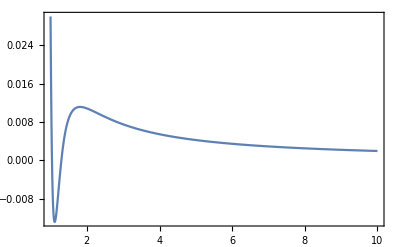

```mathematica
Plot[τ[r]/.SOLOUT,{r,1.0001,10}]
```

```mathematica
M
```

0.269848

```mathematica
ScalarProfile[0.03,0.272962040068167,3]
```

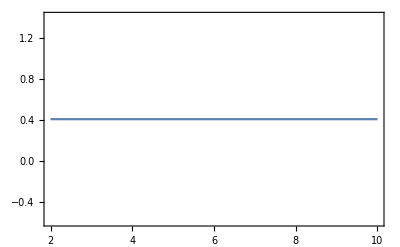

```mathematica
Plot[{ArcTan[ξ[r]/τ[r]]/.SOLOUT},{r,2,10}]
```

```mathematica
IntOut[0.35,0.35,0.2729,3]
```

0.000100384

```mathematica
M
```

0.92717

```mathematica
Qτ+Qξ
```

0.73443

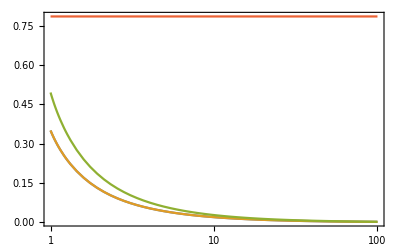

{0.927036,0.73443}

```mathematica
ScalarProfile[0.35,0.35,0.272962040068167,3]
{M,Qτ+Qξ}
```

```mathematica
IntOut[0.7,0.7,0.27,2]
```

-0.0556965

```mathematica
ShootingAlpha[0.7,2,0.27]
```

0.264628

```mathematica
ScalarProfile[0.7,0.2646275466068468,2]
{M,Qτ+Qξ}
```

{-Graphics- -Graphics-}

{0.97382+0.0000180902 ⅈ,1.21107+0.000635169 ⅈ}

```mathematica
IntOut[0.2,0.28,5]
```

0.000661968

```mathematica
Plot[Re[τ[r]]/.SOLOUT,{r,rInit,100}]
```

-Graphics-

```mathematica
ShootingAlpha[0.2,5,0.28]
```

0.280857

```mathematica
ScalarProfile[0.2,0.28085743505284594,5]
{M,Qτ+Qξ}
```

{-Graphics- -Graphics-}

{0.915146,0.433507}

For same initial value, single field case has M ≂ 1.00. Here M ≂ 0.95.

### Look for M≂1 solutions for β=2 , 5

```mathematica
ShootingAlpha[0.48,0.48,2,0.24]
M
```

0.237594

1.01392

```mathematica
ScalarProfile[0.48,0.48,0.2375937900170501,2]
```

{-Graphics- -Graphics-}

```mathematica
ShootingAlpha[0.15,0.15,5,0.24]
M
```

0.238215

1.00583

```mathematica
ScalarProfile[0.15,0.15,0.23821505936857965,5]
```

{-Graphics- -Graphics-}

### τh = 2 ξh

```mathematica
ShootingAlpha[0.4,0.2,2,0.24]
```

0.209353

```mathematica
IntOut[0.4,0.2,0.209353,2]
```

4.57634×10^-7

```mathematica
LogLinearPlot[{ξ[r]/.SOLOUT,τ[r]/.SOLOUT},{r,1,100}]
{M,Qτ,Qξ}
```

-Graphics-

{1.08247,0.416742,0.208371}

```mathematica
ScalarProfile[0.4,0.2,0.20935334747227088,2]
```

{-Graphics-}

### τh = 5 ξh

```mathematica
ShootingAlpha[0.5,0.1,2,0.24]
```

0.216657

```mathematica
IntOut[0.5,0.1,0.2166570192676626,2]
```

7.96455×10^-12

```mathematica
LogLinearPlot[{ξ[r]/.SOLOUT,τ[r]/.SOLOUT},{r,1,100}]
{M,Qτ,Qξ}
```

-Graphics-

{1.06259,0.517126,0.103425}

```mathematica
ScalarProfile[0.5,0.1,0.2166570192676626,2]
```

{-Graphics-,-Graphics-}

{1.08247,0.416742,0.208371}

## Q-M Plots τh=ξh

### τh=ξh

#### β=0

```mathematica
ShootingAlpha[0.65,0.65,0,0.19]
```

$Aborted

```mathematica
beta0Table = Table[ScalarQM[0,phi,phi,0.18],{phi,0.01,0.54,0.02}]
```

{{{0.181973},{1.17215,0.0105439},{1.17215,0.0105439}},{{0.181932},{1.17262,0.03162},{1.17262,0.03162}},{{0.18185},{1.17357,0.0526612},{1.17357,0.0526612}},{{0.181727},{1.17499,0.0736438},{1.17499,0.0736438}},{{0.181563},{1.17689,0.0945437},{1.17689,0.0945437}},{{0.181358},{1.17925,0.115336},{1.17925,0.115336}},{{0.181112},{1.18209,0.135996},{1.18209,0.135996}},{{0.180826},{1.18541,0.156495},{1.18541,0.156495}},{{0.180499},{1.18919,0.176806},{1.18919,0.176806}},{{0.180132},{1.19344,0.196898},{1.19344,0.196898}},{{0.179725},{1.19816,0.216738},{1.19816,0.216738}},{{0.179279},{1.20335,0.236291},{1.20335,0.236291}},{{0.178795},{1.209,0.255514},{1.209,0.255514}},{{0.178272},{1.21511,0.274363},{1.21511,0.274363}},{{0.177713},{1.22168,0.292783},{1.22168,0.292783}},{{0.177119},{1.22869,0.310708},{1.22869,0.310708}},{{0.176494},{1.23615,0.328057},{1.23615,0.328057}},{{0.175841},{1.24401,0.34472},{1.24401,0.34472}},{{0.175171},{1.25227,0.360542},{1.25227,0.360542}},{{0.174503},{1.26084,0.375262},{1.26084,0.375262}},{{0.173903},{1.26954,0.388289},{1.26954,0.388289}},{{0.173538},{1.27756+0.0000341006 ⅈ,0.398001+0.00144899 ⅈ},{1.27756+0.0000341006 ⅈ,0.398001+0.00144899 ⅈ}},{{0.172748},{1.2874+0.000276184 ⅈ,0.407398+0.00573989 ⅈ},{1.2874+0.000276184 ⅈ,0.407398+0.00573989 ⅈ}},{{0.171576},{1.2989+0.000608514 ⅈ,0.417364+0.0118013 ⅈ},{1.2989+0.000608514 ⅈ,0.417364+0.0118013 ⅈ}},{{0.170143},{1.31166+0.000960704 ⅈ,0.428012+0.0191709 ⅈ},{1.31166+0.000960704 ⅈ,0.428012+0.0191709 ⅈ}},{{0.16854},{1.32532+0.00128298 ⅈ,0.439355+0.0275728 ⅈ},{1.32532+0.00128298 ⅈ,0.439355+0.0275728 ⅈ}},{{0.166831},{1.33968+0.0015275 ⅈ,0.451377+0.0368243 ⅈ},{1.33968+0.0015275 ⅈ,0.451377+0.0368243 ⅈ}}}

```mathematica
beta0Double = beta0Table[[;;,2]]
ListPlot[Re[beta0Double]]
```

{{1.17215,0.0105439},{1.17262,0.03162},{1.17357,0.0526612},{1.17499,0.0736438},{1.17689,0.0945437},{1.17925,0.115336},{1.18209,0.135996},{1.18541,0.156495},{1.18919,0.176806},{1.19344,0.196898},{1.19816,0.216738},{1.20335,0.236291},{1.209,0.255514},{1.21511,0.274363},{1.22168,0.292783},{1.22869,0.310708},{1.23615,0.328057},{1.24401,0.34472},{1.25227,0.360542},{1.26084,0.375262},{1.26954,0.388289},{1.27756+0.0000341006 ⅈ,0.398001+0.00144899 ⅈ},{1.2874+0.000276184 ⅈ,0.407398+0.00573989 ⅈ},{1.2989+0.000608514 ⅈ,0.417364+0.0118013 ⅈ},{1.31166+0.000960704 ⅈ,0.428012+0.0191709 ⅈ},{1.32532+0.00128298 ⅈ,0.439355+0.0275728 ⅈ},{1.33968+0.0015275 ⅈ,0.451377+0.0368243 ⅈ}}

-Graphics-

#### β=1

```mathematica
ShootingAlpha[0.55,0.55,1,0.18]
```

0.181153

```mathematica
beta1Table = Table[ScalarQM[1,phi,phi,0.18],{phi,0.01,0.6,0.02}]
```

{{{0.181979},{1.1721,0.010544},{1.1721,0.010544}},{{0.181986},{1.17218,0.0316238},{1.17218,0.0316238}},{{0.181999},{1.17236,0.0526785},{1.17236,0.0526785}},{{0.182018},{1.17262,0.0736916},{1.17262,0.0736916}},{{0.182043},{1.17297,0.094646},{1.17297,0.094646}},{{0.182073},{1.17341,0.115525},{1.17341,0.115525}},{{0.182108},{1.17395,0.13631},{1.17395,0.13631}},{{0.182145},{1.17458,0.156984},{1.17458,0.156984}},{{0.182186},{1.17532,0.177529},{1.17532,0.177529}},{{0.182227},{1.17617,0.197926},{1.17617,0.197926}},{{0.182268},{1.17712,0.218154},{1.17712,0.218154}},{{0.182307},{1.1782,0.238194},{1.1782,0.238194}},{{0.182344},{1.17939,0.258025},{1.17939,0.258025}},{{0.182375},{1.18072,0.277624},{1.18072,0.277624}},{{0.182399},{1.18218,0.296968},{1.18218,0.296968}},{{0.182414},{1.18378,0.316031},{1.18378,0.316031}},{{0.182418},{1.18553,0.334788},{1.18553,0.334788}},{{0.18241},{1.18744,0.353208},{1.18744,0.353208}},{{0.182385},{1.18951,0.371262},{1.18951,0.371262}},{{0.182343},{1.19175,0.388914},{1.19175,0.388914}},{{0.182281},{1.19417,0.406126},{1.19417,0.406126}},{{0.182197},{1.19678,0.422853},{1.19678,0.422853}},{{0.182088},{1.19957,0.439046},{1.19957,0.439046}},{{0.181952},{1.20255,0.454641},{1.20255,0.454641}},{{0.181789},{1.20574,0.469562},{1.20574,0.469562}},{{0.181598},{1.20912,0.483705},{1.20912,0.483705}},{{0.181383},{1.21268,0.496914},{1.21268,0.496914}},{{0.181153},{1.21639,0.508913},{1.21639,0.508913}},{{0.180988},{1.22-0.0000130482 ⅈ,0.518736+0.000109833 ⅈ},{1.22-0.0000130482 ⅈ,0.518736+0.000109833 ⅈ}},{{0.180759},{1.22388-0.000060515 ⅈ,0.526563+0.00214191 ⅈ},{1.22388-0.000060515 ⅈ,0.526563+0.00214191 ⅈ}}}

```mathematica
beta1Double = beta1Table[[;;,2]];
ListPlot[Re[beta1Double]]
```

-Graphics-

#### β =2

```mathematica
ShootingAlpha[0.5,2,0.2]
```

0.241016

```mathematica
beta2Table = Table[ScalarQM[2,phi,0.24],{phi,0.01,0.7,0.02}]
```

{{{0.182008},{1.17198,0.0105444},{1.17198,0.0105444}},{{0.182243},{1.17109,0.0316331},{1.17109,0.0316331}},{{0.182713},{1.16934,0.0527214},{1.16934,0.0527214}},{{0.183416},{1.16673,0.0738082},{1.16673,0.0738082}},{{0.18435},{1.16328,0.0948907},{1.16328,0.0948907}},{{0.185512},{1.15905,0.115964},{1.15905,0.115964}},{{0.186899},{1.15406,0.137022},{1.15406,0.137022}},{{0.188506},{1.14837,0.158055},{1.14837,0.158055}},{{0.190326},{1.14203,0.17905},{1.14203,0.17905}},{{0.192355},{1.13511,0.199991},{1.13511,0.199991}},{{0.194583},{1.12767,0.22086},{1.12767,0.22086}},{{0.197003},{1.11979,0.241635},{1.11979,0.241635}},{{0.199604},{1.11153,0.262291},{1.11153,0.262291}},{{0.202374},{1.10297,0.282799},{1.10297,0.282799}},{{0.205301},{1.09419,0.30313},{1.09419,0.30313}},{{0.208371},{1.08527,0.323248},{1.08527,0.323248}},{{0.211568},{1.07628,0.343117},{1.07628,0.343117}},{{0.214874},{1.0673,0.362699},{1.0673,0.362699}},{{0.218272},{1.0584,0.381954},{1.0584,0.381954}},{{0.22174},{1.04963,0.400836},{1.04963,0.400836}},{{0.225256},{1.04108,0.419302},{1.04108,0.419302}},{{0.228798},{1.03284,0.437305},{1.03284,0.437305}},{{0.23234},{1.02496,0.454795},{1.02496,0.454795}},{{0.235855},{1.01748,0.471722},{1.01748,0.471722}},{{0.239315},{1.01047,0.488034},{1.01047,0.488034}},{{0.242692},{1.00397,0.503677},{1.00397,0.503677}},{{0.245955},{0.998026,0.518595},{0.998026,0.518595}},{{0.249073},{0.992677,0.532731},{0.992677,0.532731}},{{0.252014},{0.987955,0.546024},{0.987955,0.546024}},{{0.254747},{0.983885,0.558409},{0.983885,0.558409}},{{0.257241},{0.980489,0.569816},{0.980489,0.569816}},{{0.259464},{0.977779,0.580163},{0.977779,0.580163}},{{0.261385},{0.975746,0.589348},{0.975746,0.589348}},{{0.262973},{0.974455,0.597218},{0.974455,0.597218}},{{0.264188},{0.973835,0.603432},{0.973835,0.603432}}}

```mathematica
beta2Double = beta2Table[[;;,2]]
```

{{1.17198,0.0105444},{1.17109,0.0316331},{1.16934,0.0527214},{1.16673,0.0738082},{1.16328,0.0948907},{1.15905,0.115964},{1.15406,0.137022},{1.14837,0.158055},{1.14203,0.17905},{1.13511,0.199991},{1.12767,0.22086},{1.11979,0.241635},{1.11153,0.262291},{1.10297,0.282799},{1.09419,0.30313},{1.08527,0.323248},{1.07628,0.343117},{1.0673,0.362699},{1.0584,0.381954},{1.04963,0.400836},{1.04108,0.419302},{1.03284,0.437305},{1.02496,0.454795},{1.01748,0.471722},{1.01047,0.488034},{1.00397,0.503677},{0.998026,0.518595},{0.992677,0.532731},{0.987955,0.546024},{0.983885,0.558409},{0.980489,0.569816},{0.977779,0.580163},{0.975746,0.589348},{0.974455,0.597218},{0.973835,0.603432}}

```mathematica
ListPlot[beta2Double]
```

-Graphics-

#### β=5

```mathematica
ShootingAlpha[0.2,5,0.24]
```

0.280857

```mathematica
beta5Table = Table[ScalarQM[5,phi,0.28],{phi,0.01,0.3,0.02}]
```

{{{0.182229},{1.17118,0.0105467},{1.17118,0.0105467}},{{0.184238},{1.16396,0.0316932},{1.16396,0.0316932}},{{0.188257},{1.14986,0.0529866},{1.14986,0.0529866}},{{0.194286},{1.12954,0.0744854},{1.12954,0.0744854}},{{0.202321},{1.1039,0.0962027},{1.1039,0.0962027}},{{0.212344},{1.074,0.118107},{1.074,0.118107}},{{0.224324},{1.04095,0.14013},{1.04095,0.14013}},{{0.238215},{1.00583,0.162182},{1.00583,0.162182}},{{0.253956},{0.969637,0.18416},{0.969637,0.18416}},{{0.271468},{0.933215,0.205957},{0.933215,0.205957}},{{0.290651},{0.897274,0.227465},{0.897274,0.227465}},{{0.311387},{0.862379,0.248581},{0.862379,0.248581}},{{0.333528},{0.828968,0.269202},{0.828968,0.269202}},{{0.356898},{0.797373,0.289226},{0.797373,0.289226}},{{0.381285},{0.767837,0.30855},{0.767837,0.30855}}}

```mathematica
beta5Double=beta5Table[[;;,2]]
```

{{1.17118,0.0105467},{1.16396,0.0316932},{1.14986,0.0529866},{1.12954,0.0744854},{1.1039,0.0962027},{1.074,0.118107},{1.04095,0.14013},{1.00583,0.162182},{0.969637,0.18416},{0.933215,0.205957},{0.897274,0.227465},{0.862379,0.248581},{0.828968,0.269202},{0.797373,0.289226},{0.767837,0.30855}}

```mathematica
ListPlot[beta5Double]
```

-Graphics-

```mathematica
Export["Plots/Doublebeta0.txt",beta0Double,"Table"]
Export["Plots/Doublebeta1.txt",beta1Double,"Table"]
Export["Plots/Doublebeta2.txt",beta2Double,"Table"]
Export["Plots/Doublebeta5.txt",beta5Double,"Table"]
```

Plots/Doublebeta0.txt

Plots/Doublebeta1.txt

Plots/Doublebeta2.txt

Plots/Doublebeta5.txt

### τh^2 + ξh^2=ϕh^2 and β=3

```mathematica
θ=π/3;
S=ScalarQM[3,0.25Cos[θ],0.25 Sin[θ],0.2];
√(S[[2,2]]^2+S[[3,2]]^2)
```

0.266166

```mathematica
θ=π/6;
S=ScalarQM[3,0.25Cos[θ],0.25 Sin[θ],0.2];
√(S[[2,2]]^2+S[[3,2]]^2)
```

0.266166

```mathematica
θ=π/4;
S=ScalarQM[3,0.25Cos[θ],0.25 Sin[θ],0.2];
√(S[[2,2]]^2+S[[3,2]]^2)
```

0.266166

```mathematica
θ=π/7;
S=ScalarQM[3,0.25Cos[θ],0.25 Sin[θ],0.2];
√(S[[2,2]]^2+S[[3,2]]^2)
```

0.266166

```mathematica
S=ScalarQM[3,0.5,0.25,0.2];
{S[[2,1]],√(S[[2,2]]^2+S[[3,2]]^2)}
```

{0.889576,0.578278}

```mathematica
NormCharge[θ_,β_,ϕc_,guess_]:=(
S =ScalarQM[β,ϕc Cos[θ],ϕc Sin[θ],guess];
{S[[2,1]],√(S[[2,2]]^2+S[[3,2]]^2)}
);
```

```mathematica
NormChargeDouble[θ_,β_,ϕc_,guess_]:=(
S =ScalarQM[β,ϕc Cos[θ],ϕc Sin[θ],guess];
{{S[[2,1]],S[[2,2]]},{S[[2,1]],S[[3,2]]}}
);
```

```mathematica
NormChargeRatio[R_,β_,ϕc_,guess_]:=(
S =ScalarQM[β,ϕc,R ϕc,guess];
{S[[2,1]],√(S[[2,2]]^2+S[[3,2]]^2)}
);
```

```mathematica
NormCharge[π/3,2,0.5,0.24]
```

{1.06571,0.517808}

```mathematica
θ=π/3;Beta2=Table[NormChargeDouble[π/3,3,phi,0.3],{phi,0.01,0.8,0.05}]
```

{{{1.17194,0.00527233},{1.17194,0.00913194}},{{1.16664,0.0316623},{1.16664,0.0548406}},{{1.15407,0.0581618},{1.15407,0.100739}},{{1.13493,0.084817},{1.13493,0.146907}},{{1.11026,0.111609},{1.11026,0.193312}},{{1.0813,0.138448},{1.0813,0.2398}},{{1.04941,0.165186},{1.04941,0.28611}},{{1.01595,0.191625},{1.01595,0.331904}},{{0.982164,0.217538},{0.982164,0.376786}},{{0.949156,0.242676},{0.949156,0.420327}},{{0.91786,0.266778},{0.91786,0.462073}},{{0.889037,0.289573},{0.889037,0.501555}},{{0.863281,0.310782},{0.863281,0.538291}},{{0.841037,0.330127},{0.841037,0.571798}},{{0.822601,0.347333},{0.822601,0.601598}},{{0.808131,0.362139},{0.808131,0.627243}}}

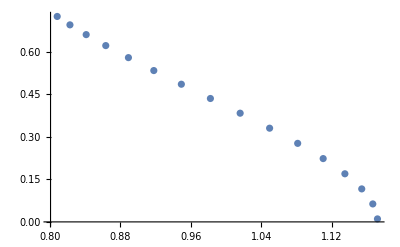

```mathematica
ListPlot[Re[%]]
```

```mathematica
Beta2A=Table[NormChargeRatio[2,2,phi,0.24],{phi,0.01,0.8,0.05}]
```

$Aborted

## Q-M Symmetry

Fix ϕh, compare with τh^2+ξh^2=ϕh^2

```mathematica
ScalarQM[2,0.25,0,0.2]
```

{{0.190991},{1.13975,0.263259},{1.13975,0.}}

{{0.240164},{1.0088,0.602561},{1.0088,0.347889}}

0.695778

0.523599

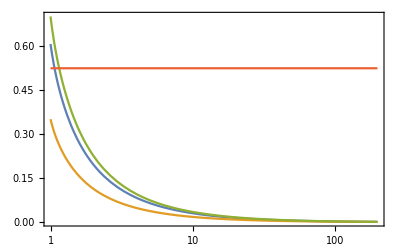

```mathematica
ϕP=0.7;
θ=π/6;
ScalarQM[2,ϕP × Cos[θ],ϕP × Sin[θ],0.24]
√(Qξ^2+Qτ^2)
ArcTan[(ξ[100]/τ[100])/.SOLOUT]
ScalarProfile[ϕP × Cos[θ],ϕP × Sin[θ],0.240164,2]
```

```mathematica
M
```

1.0088

ScalarProfile[ϕP Cos[θ],ϕP Sin[θ],0.190991,2]

```mathematica
N[π/5]
```

0.628319

Explore the symmetry

(τ_h
ξ_h)→ ±(Cos[θ] | -Sin[θ]
Sin[θ] | Cos[θ])(τ_h
ξ_h).

```mathematica
ScalarQM[2,0.25,0.35,0.207]
√(Qξ^2+Qτ^2)
```

{{0.207457},{1.0879,0.260881},{1.0879,0.365233}}

0.448836

```mathematica
θ=π/8;
τI = 0.25;
ξI = 0.35;
ScalarQM[2,(τI*Cos[θ]-ξI*Sin[θ]),(τI*Sin[θ]+ξI*Cos[θ]),0.207]
√(Qξ^2+Qτ^2)
```

{{0.207457},{1.0879,0.101254},{1.0879,0.437266}}

0.448836

```mathematica
ScalarProfile[0.35,0.35,0.272962040068167,3]
```